This file contains codes for the parameters used, the model definitions, the initial conditions, and  plotting the results. 

- Miscellaneous contains some parameters (color for aspen, image size and plot style etc.), contour plots for fire rotation, and function used throughout 
- Initial conditions generates the initial conditions for the simulations. The process of generating the initial conditions actually depends on the parameters ,  but due to the iterative process and to make the sequence natural, the initial conditions section is presented early.
- Parameters used throughout. There are separated into symmetric and asymmetric. Only the asymmetric and more realistic scenario will be shown in the main text, the symmetric is in the supplements. Notice that the parameters are framed as a Dataset, that makes it easier to obtain the values using key (type and species, and which parameters) to plug into the model definitions
 
 Sections that starts with Figure are used to define and generate the figures. They generally contained the same subsections: Model definition, Visualization, and Recycle.
- Model definition generates the text file used as input for the C++ code and the code used to run all the parameter combinations. The core of the text file is the same, but the parameters can change depending on the figures. See CHTC of UW-Madison for the details of the implementations. When the simulation is run on a normal computer, the bash code is also included in Model definition
- Visualization plots the figures. Sometimes, additional plots are shown to make sure the model does not produce strange results. 
- Recycle contains codes used in previous versions of the manuscript. Generally they show different plots (e.g., proportion of area burned or tree densities for each species).

In figure 4 and 5, an additional section: Compile data is included. Compile data takes the output of the simulation, extract the key statistics, and export the results as a csv. It is simpler play with the figures with the compiled data compared to the raw ones.

- The section Grouping figures are just to facilitate the compilations of the figures.

The Supplementary analyses and figures include model for both pines (aspen is not included), testing the model mixed forest with a different initial condition: aspen root is removed to mimic the seedling establishment of aspen. The last section Old Figure 4 is slice of the contour plot.

```mathematica
(*Color used for the aspen, is5 is image size*)
```

```mathematica
colA = ColorData[105][1];
is5 = 3 72;
```

```mathematica
(* layout to show the contours for fire rotation*)
```

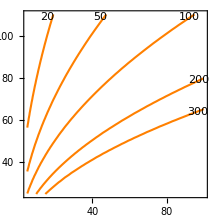

```mathematica
cc = ContourPlot[1/(rr^2 Pi/200^2)ffi,{ffi,5,100},{rr,25,110}, Contours->{20,50,100,200,300 },ContourLabels->(Text[#3,{#1-3,#2-1},Background->White]&),ContourStyle->Directive[AbsoluteThickness[1.5],Orange],ContourShading-> None,LabelStyle->Directive[14,Opacity[0]], ImageSize->is5 ]
```

```mathematica
(* A function that converts proportion of area burned to radius (for y axis in the plot) *)
PropToRad [dat_]:= Module[{result = dat}, result[[All,2]]  = Sqrt[200.^2 result[[All,2]]/Pi]; result ];
```

```mathematica
SetDirectory["/Users/tanjona/Documents/asa/projects/ACES_goldilocks/code"]
```

/Users/tanjona/Documents/asa/projects/ACES_goldilocks/code

## Initial initial conditions

```mathematica
(* Generate random initial conditions, this is used to generate the true initial conditions. *)
U = 200;
SeedRandom[1];
LL  =2000;
PN0 =  {ConstantArray[1,LL],RandomReal[{0,U},LL],RandomReal[{0,U},LL]}//Transpose;
PS0 =  {ConstantArray[4,LL],RandomReal[{0,U},LL],RandomReal[{0,U},LL]}//Transpose;
AA0 =  {ConstantArray[9,LL],RandomReal[{0,U},LL],RandomReal[{0,U},LL]}//Transpose;
```

```mathematica
Export["inital_condition/PN0.txt",PN0,"Table"];
Export["inital_condition/PS0.txt",PS0,"Table"];
Export["inital_condition/AA0.txt",AA0,"Table"];
```

### Initial conditions with competitions

```mathematica
iPN = Import["fig3/snp/fig3_asym_com_PN0_init", "Table"];
iPS = Import["fig3/snp/fig3_asym_com_PS0_init", "Table"];
iAA = Import["fig3/snp/fig3_asym_com_AA0_init", "Table"];
```

Import::nffil: File fig3/snp/fig3_asym_com_PN0_init not found during Import.

Import::nffil: File fig3/snp/fig3_asym_com_PS0_init not found during Import.

Import::nffil: File fig3/snp/fig3_asym_com_AA0_init not found during Import.

```mathematica
(* This tally the total number in the individuals for each type *)
idiPN = Sort@Tally[iPN[[All,1]]];
idiPS = Sort@Tally[iPS[[All,1]]];
idiAA = Sort@Tally[iAA[[All,1]]];
```

```mathematica
idiPN
```

{{1,2075},{2,3944},{3,6229}}

```mathematica
idiPS
```

{{4,280},{5,1052},{6,837},{7,1316}}

#### For both lodgepole pine

```mathematica
(*Calculate the proportion of non-serotinous tree *)
fPP = (6229 - 1316)/6229.
```

0.78873

```mathematica
(* use the proprotion to sample individuals in each stage *)
iPP = iPS;
gPN = GroupBy[iPN,First];
Do[
temp = RandomSample[gPN[i],Ceiling[fPP idiPN[[i,2]]]];
iPP = Join[iPP, temp];
,{i,3}];
```

```mathematica
Export["init_com_PP.txt",iPP, "Table"];
```

#### For all species

```mathematica
idiPN[[All,2]]
```

{2075,3944,6229}

```mathematica
idiPS[[All,2]]
```

{280,1052,837,1316}

```mathematica
idiAA[[All,2]]
```

{7326,5524,2959}

```mathematica
treeS = idiPS[[{3,4},2]]//Total (* number of serotinous tree *)
```

2153

```mathematica
numP = 0.9 idiPN[[3,2]] ; (* number of non-serotinous pine 90% *)
treeN = numP- treeS; (* number of non-serotinous pine*)
freqN = treeN/idiPN[[3,2]]//N; (* calculates the frequency non-serotinous pine for the tree *)
nPN= #{1,freqN} &/@idiPN//Ceiling; (* frequency of non-serotinous for each stage*)

numA = 0.1 idiPN[[3,2]]; (* number of aspen 10% *)
freqA = numA/idiAA[[2,2]] ; (* frequency of aspen tree *)
nAA= #{1,freqA} &/@idiAA//Ceiling; (*frequency of aspen for each stage*)
```

```mathematica
(* number of individuals in each stage for the serotinous pine *)
nPS = idiPS
```

{{4,280},{5,1052},{6,837},{7,1316}}

```mathematica
(* just checking the values *)
```

```mathematica
nPN[[3,2]] + nPS[[3,2]] +nPS[[4,2]] + nAA[[2,2]]
```

6230

```mathematica
nPN[[All,2]]/idiPN[[All,2]]//N
```

{0.554699,0.554513,0.554503}

```mathematica
nAA[[All,2]]/ idiAA[[All,2]]//N
```

{0.112886,0.112781,0.112876}

```mathematica
(* using association so I can use the key to identify each stage*)
```

```mathematica
ALL = Join[iPN,iAA];
key = Association[#[[1]]->#[[2]]& /@ Join[nPN,nAA]];
```

```mathematica
key
```

{1→1151,2→2187,3→3454,9→827,10→623,11→334}

```mathematica
gAll = GroupBy[ALL,First];
```

```mathematica
gAll//Keys
```

{3,2,1,10,11,9}

```mathematica
key[1]
```

1151

```mathematica
(* sample the individuals to merge with the serotinous data *)
RR = gAll//Keys;
newINIT = {};
Do[
temp = RandomSample[ gAll[i],key[i] ];
newINIT = Join[newINIT,temp];
,{i,RR}];
```

```mathematica
(* join the serotinous data and the sampled aspen and non-serotinous pine *)
newINIT = Join[newINIT,iPS];
```

```mathematica
Tally[newINIT[[All,1]]]
```

{{3,3454},{2,2187},{1,1151},{10,623},{11,334},{9,827},{7,1316},{6,837},{5,1052},{4,280}}

```mathematica
Export["init_com_ALL.txt",newINIT, "Table"];
```

#### Removing roots for aspen

```mathematica
(*A residual code where aspen roots were removed *)
```

```mathematica
DeleteCases[test, x_ /; x[[1]]==1]
```

{{2,3},{2,3},{3,4},{4,5}}

```mathematica
dat = Import["init_com_ALL.txt","Table"];
```

```mathematica
dat2 = DeleteCases[dat,  x_ /; x[[1]]==11]
```

```mathematica
Export["init_com_AllnoRoot.txt",dat2, "Table"]
```

## Parameters

The parameters here are used extensively later to define the model. The whole point is to use the association data formation in Mathematica to call on different parameters by the keys. For instance  SPMT[“n1”, “MI”] gives the intrinsic mortality rate of an individual called n1. 

There are two sets of parameters, one for the symmetric and one for the (default) asymmetric

```mathematica
(* this is used so that I use letters as spID argument instead of integer *)
SpCode = {"n1"-> 1,"n2"-> 2, "n3"-> 3, "s1"-> 4, "s2"->5,"s3"->6, "s4"-> 7,"s5"-> 8 ,"a2"->9,"a3"-> 10,"a4"-> 11,"F"->0 }//Association;
(* domain size *)
U = 200;
```

### Symmetric

```mathematica
(* mortality fire, severity *)
sev = 1/(365 12 );
MF= { "F"-> sev}//Association;

(* mortality intrinsic rates*)
MI = {"n1"->4, "n2"-> 40, "n3"-> 260, "s1"->4,"s2"->40 , "s3"->60,"s4"-> 140,"s5"-> 140/365,"a2"-> 40,"a3"-> 160,"a4"-> 500,"F"-> 14/365}//Association;

(* birth rates and standard deviation, i.e., scale *)
BB = { "n3"-> 0.2, "s3"->0.2,"s5"->100, "a4"-> 0.6, "F"->FFI}//Association;
KB = {"n3"->  30,"s3"->  30,"s5"->30,"a4"-> 5,"F"->pburn}//Association;

(* stage transition rates *)
GG = {"n1"-> 3,"n2"-> 30,"s1"->  3, "s2"-> 30, "s3"-> 50,"a2"-> 30,"a3"-> 40}//Association;

(* intraspecific competition rate and standard deviation, i.e. scale denoted with K *)
MC = {"n3"->0.1, "s3"->0.1,"s4"->0.1,"a3" -> 0.1,"a4"->0.4}//Association;
KMC = {"n3"-> 1.5,"s3"-> 1.5,"s4"-> 1.5,  "a3"-> 1.5,"a4"->3}//Association;

(* inter-stage and interspecific competition rate and standard deviation, i.e. scale denoted with K *)
McC = {"AP"->0.1,"PA"->0.1,"pP"->1.,"aA"->2.,"aP"->2.,"pA"->1., "RP" -> 0.01, "PR"-> 0.01}//Association;
KMcC= {"AP"->1.5, "PA"->1.5,"pP"-> 0.75,"aA"->0.75,"aP"->0.75,"pA"->0.75, "RP" -> 3., "PR"->3.}//Association;

(* dataset for parameters with visualization, S for symmetric *)
visSPMT =  Dataset[{"m"-> MI,"g"-> GG,"b"->BB,"Kb"-> KB,"c"->MC,"Kc"-> KMC,"cC"-> McC,"KcC"->KMcC,"mF"->MF}//N//Association]//Transpose;
SPMT = Dataset[{"m"-> 1/MI,"g"-> 1/GG,"b"->BB,"Kb"-> KB,"c"->MC,"Kc"-> KMC,"cC"-> McC,"KcC"->KMcC,"mF"->1/MF}//N//Association]//Transpose;
```

### Asymmetric

```mathematica
(* birth rates and standard deviation, i.e., scale *)
BB = { "n3"-> 0.2, "s3"->0.2,"s5"->100, "a4"-> 0.6, "F"->FFI}//Association;
KB = {"n3"->  30,"s3"->  30,"s5"->30,"a4"-> 5,"F"->pburn}//Association;

(* intraspecific competition rate and standard deviation, i.e. scale denoted with K *)
MC = {"n3"->0.1, "s3"->0.1,"s4"->0.1,"a3" -> 0.08 (*this is lower*),"a4"->0.4 }//Association;
KMC = {"n3"-> 1.5,"s3"-> 1.5,"s4"-> 1.5,  "a3"-> 1.5,"a4"->3}//Association;

(* inter-stage and interspecific competition rate and standard deviation, i.e. scale denoted with K*)
McC = {"AP"->0.2,"PA"->0.05,"pP"->1.,"aA"->2.,"aP"->2.,"pA"->0.5, "RP" -> 0.1, "PR"->0.01}//Association;
KMcC= {"AP"->1.5, "PA"->1.5,"pP"-> 0.75,"aA"->0.75,"aP"->0.75,"pA"->0.75, "RP" ->3. , "PR"->3.}//Association;

(* dataset for parameters with visualization, S for symmetric *)
visAPMT =  Dataset[{"m"-> MI,"g"-> GG,"b"->BB,"Kb"-> KB,"c"->MC,"Kc"-> KMC,"cC"-> McC,"KcC"->KMcC,"mF"->MF}//N//Association]//Transpose;
APMT = Dataset[{"m"-> 1/MI,"g"-> 1/GG,"b"->BB,"Kb"-> KB,"c"->MC,"Kc"-> KMC,"cC"-> McC,"KcC"->KMcC,"mF"->1/MF}//N//Association]//Transpose;
```

## Figure 2: snapshots

```mathematica
sym =False;
If[sym ==True,
PMT = SPMT; type = "sym",
PMT = APMT;type = "asym"];
T = 50;
U =200;
Do[
TEXTSIM = {"#!/bin/bash "};
Do[
(* scaling the fire related rate with domain size *) 
scaledB =DecimalForm[1./(fri U^2)]; (*gives the per area fire occurrence*)
firerad =N@Sqrt[pburn U^2/ Pi]; (* define fire size wrt to area burn*)
scaledmF = DecimalForm[N[firerad^2 Pi PMT["F","mF"]]]; (* this is the height of the fire kernel *)

(* model definition *)
text= 
{
(* for non-serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["n1","n3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n2","n1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n3","n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["n1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","n3","pP"],

(* for serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s2","s1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s3","s2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s4","s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["s1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s3","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s4","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","s4"],

(* for aspen without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["a2","a4"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a3","a2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a4","a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["a2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","a3","aA"],

(* interspecific competition *)
(* between adult pines *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s4","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s4"],
(* adult pine to juvenile and adult aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","n3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","n3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s4","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s4","AP"],
(* adult aspen to juveline and adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a3","PA"],

(* fire *)
Immigration[SpCode[#],scaledB]&["F"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["F"],

(* non-serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n3","F"],

(* serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s3","F"],
ChangeToAnotherTypeByCombustion[SpCode[#1],SpCode[#2],SpCode[#3],tophat[scaledmF,firerad]]&["s5","s4","F"],
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s5"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["s5"],

(* aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a3","F"]
};

text=Map[ToString,text];
Export["fig2/model_"<>type<>"_p_"<>ToString@pburn<>"_FRI_"<>ToString@fri<>"_U_"<>ToString@U<>".txt",text];

Do[
textsim  = 
"time ./goldilocks_sim -p processes.txt -m model_"<>type<>"_p_"<>ToString@pburn<>"_FRI_"<>ToString@fri<>"_U_"<>ToString@U<>".txt -i fig3_"<>type<>"_"<>com<>"0_000502 -oute 0 -outc 0 -o fig2_"<>type<>"_com_"<>com<>"_p_"<>ToString@pburn<>"_FRI_"<>ToString@fri<>"_U_"<>ToString@U<>"_rep_"<>ToString@rep<>" -r "<>ToString@rep<>" -U "<>ToString@U<>" -T "<>ToString@T<>" -dT 0.5 -w "<>ToString[30]<>" -osep snp/fig2_snp_"<>type<>"_"<>com<>"_rep_"<>ToString@rep<>"_";
AppendTo[TEXTSIM,textsim];
,{com,{"PN","PS","AA"}}];

,{fri ,{20}},{pburn,{0.6}}];
Export["fig2/fig2_"<>type<>"_sim_rep_"<>ToString@rep<>"_U_"<>ToString@U<>".txt",TEXTSIM];
,{rep,{3}}];
Clear[PMT];
```

```mathematica
p1 = ToString@0.6;
p2 = ToString@20;
p3 = ToString@3;
dat2n = Transpose[Import["fig2/fig2_asym_com_PN_p_"<>p1<>"_FRI_"<>p2<>"_U_200_rep_"<>p3<>".counts"][[2;;,{4,5,6}]]];
dat2s = Transpose[Import["fig2/fig2_asym_com_PS_p_"<>p1<>"_FRI_"<>p2<>"_U_200_rep_"<>p3<>".counts"][[2;;,{7,8,9,10,11}]]];
dat2a = Transpose[Import["fig2/fig2_asym_com_AA_p_"<>p1<>"_FRI_"<>p2<>"_U_200_rep_"<>p3<>".counts"][[2;;,{12,13,14}]]];
```

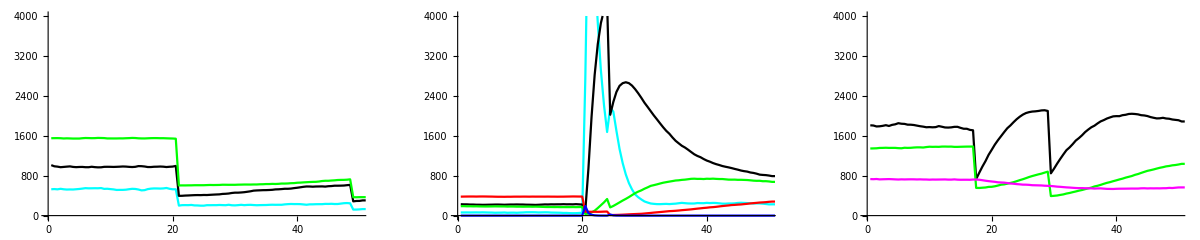

```mathematica
is = ImageSize->{Automatic,(2 72)};
fr = Frame ->  {{True,False},{True, False}};
ftx = FrameTicks-> {Automatic,{Range[0,100,20],Range[0,50,10]}//Transpose};
tx = Ticks->{{Range[0,100,20],Range[0,50,10]}//Transpose,Automatic};
pr = PlotRange->{{0,100},{0,4000}};
fign = ListLinePlot[dat2n/4,pr,PlotStyle->{Cyan,Black, Green},LabelStyle->{Black,12},is,tx];
figs = ListLinePlot[dat2s/4,pr,PlotStyle->{Cyan,Black, Green,Red,Blue},LabelStyle->{Black,12},is,tx];
figa = ListPlot[dat2a/4,pr,Joined->True,PlotStyle->{Black,Green,Magenta},LabelStyle->{Black,12},is,tx];
GraphicsRow[{fign,figs,figa}]
```

```mathematica
lg2 = LineLegend[{Cyan,Black,Green,Red,Blue,Magenta},{"Seedling", "Sapling or respourt","Adult (all species)","Unreproductive adult serotinous","Reproductive adult serotinous","Aspen root"}]
```

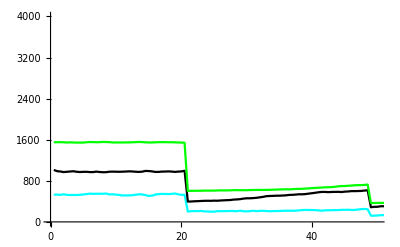

```mathematica
ListLinePlot[dat2n/4,pr,PlotStyle->{Cyan,Black, Green},LabelStyle->{Black,12},is,tx]
```

```mathematica
x0 = 18; SZ = 50;ao = AxesOrigin->{x0,x0};
pr2 =PlotRange->{{x0,x0 +SZ},{x0,x0+SZ}};
ls2 = LabelStyle->Directive[14, FontFamily->"Arial",Black];
prp2 = PlotRangePadding->Scaled[.0];

preN = Import["fig2/snp/fig2_snp_asym_PN_rep_3_000040","Table"]; 
snpN = GroupBy[preN,First][[All,All,{2,3}]];
fig2a = ListPlot[{snpN[SpCode["n1"]],(*snpN[SpCode["n2"]],*)snpN[SpCode["n3"]]},pr2,ao,AspectRatio->1,PlotMarkers->{{"×",10},(*{●,5},*){●,10}},PlotStyle->{Gray,(*White,*)Gray},Frame->True,ls2,prp2];

preN2 =Import["fig2/snp/fig2_snp_asym_PN_rep_3_000044","Table"]; 
snpN2 = GroupBy[preN2,First][[All,All,{2,3}]];
fig2b = ListPlot[{snpN2[SpCode["n1"]],(*snpN2[SpCode["n2"]],*)snpN2[SpCode["n3"]]},pr2,ao,AspectRatio->1,PlotMarkers->{{"×",10},(*{●,5},*){●,10}},PlotStyle->{Gray,(*White,*)Gray},Frame->True,ls2,prp2];
```

```mathematica
x0 = 45; SZ =50;
y0  = 15; ao = AxesOrigin->{x0,y0};
pr2 =PlotRange->{{x0,x0 +SZ},{y0,y0+SZ}};
ls2 = LabelStyle->Directive[14, FontFamily->"Arial",Black];
prp2 = PlotRangePadding->Scaled[.0];

preS = Import["fig2/snp/fig2_snp_asym_PS_rep_3_000040","Table"]; 
snpS = GroupBy[preS,First][[All,All,{2,3}]];
fig2c =ListPlot[{snpS[SpCode["s1"]],(*snpS[SpCode["s2"]],*)snpS[SpCode["s3"]],snpS[SpCode["s4"]]},pr2,ao,AspectRatio->1,PlotMarkers->{{"×",10},(*{●,5},*){"●",10},{"●",10}},PlotStyle->{Orange,(*White,*)Black,Black},Frame->True,ls2,prp2];

preS2 = Import["fig2/snp/fig2_snp_asym_PS_rep_3_000041","Table"]; 
snpS2 = GroupBy[preS2,First][[All,All,{2,3}]];
fig2d =ListPlot[{snpS2[SpCode["s1"]],(*snpS2[SpCode["s2"]],*)snpS2[SpCode["s3"]],snpS2[SpCode["s4"]]},pr2,ao,AspectRatio->1,PlotMarkers->{{"×",10},(*{●,5},*){"●",10},{"●",10}},PlotStyle->{Orange,(*White,*)Black,Black},Frame->True,ls2,prp2];
```

```mathematica
x0 = 18; SZ = 50;ao = AxesOrigin->{x0,x0};
pr2 =PlotRange->{{x0,x0 +SZ},{x0,x0+SZ}};
ls2 = LabelStyle->Directive[14, FontFamily->"Arial",Black];
prp2 = PlotRangePadding->Scaled[.0];

preA = Import["fig2/snp/fig2_snp_asym_AA_rep_3_000034","Table"]; 
snpA = GroupBy[preA,First][[All,All,{2,3}]];
fig2e= ListPlot[{snpA[SpCode["a2"]],snpA[SpCode["a3"]],snpA[SpCode["a4"]]},pr2,ao,AspectRatio->1,PlotMarkers->{{"●",5},{"●",10},{"◇",10}},PlotStyle->colA,Frame->True,ls2,prp2];

preA2 = Import["fig2/snp/fig2_snp_asym_AA_rep_3_000037","Table"]; 
snpA2 = GroupBy[preA2,First][[All,All,{2,3}]];
fig2f= ListPlot[{snpA2[SpCode["a2"]],snpA2[SpCode["a3"]],snpA2[SpCode["a4"]]},pr2,ao,AspectRatio->1,PlotMarkers->{{"●",5},{"●",10},{"◇",10}},PlotStyle->colA,Frame->True,ls2,prp2];
```

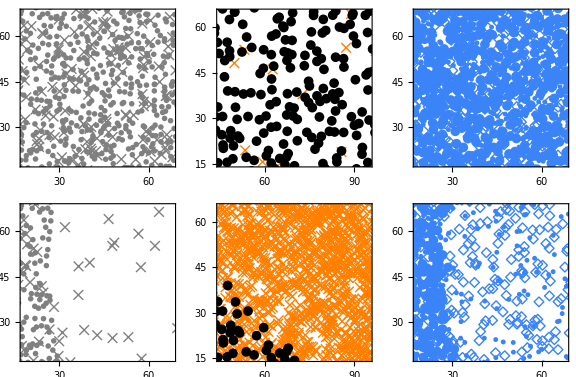

```mathematica
fig2 = GraphicsGrid[{{fig2a,fig2c,fig2e},{fig2b,fig2d,fig2f}},ImageSize->Large]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/Fig2.jpg",fig2, ImageResolution->200]
```

/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/Fig2.jpg

```mathematica
PointLegend[{Gray, Gray},{"Seedling","Tree"},LegendMarkers->{{"×",10},(*{●,5},*){●,10}}]
```

```mathematica
PointLegend[{Orange, Black},{"Seedling","Tree"},LegendMarkers->{{"×",10},(*{●,5},*){●,10}}]
```

```mathematica
PointLegend[{colA, colA,colA},{"Resprout","Tree","Root"},LegendMarkers->{{●,5},{●,10},{◇,10}}]
```

```mathematica
dat2n = Transpose[Import["fig2/fig2_asym_com_PN_p_0.8_FRI_20_U_200_rep_2.counts"][[2;;,{4,5,6}]]];
dat2s = Transpose[Import["fig2/fig2_asym_com_PS_p_0.8_FRI_20_U_200_rep_2.counts"][[2;;,{7,8,9,10,11}]]];
dat2a = Transpose[Import["fig2/fig2_asym_com_AA_p_0.8_FRI_20_U_200_rep_2.counts"][[2;;,{12,13,14}]]];
```

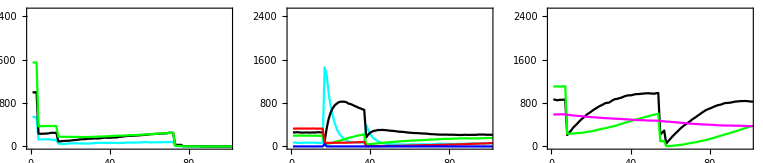

```mathematica
is = ImageSize->{Automatic,(2 72)};
fr = Frame ->  {{True,False},{True, False}};
ftx = FrameTicks-> {Automatic,False};
pr = PlotRange->{{0,100},{0,2500}};
fign = ListLinePlot[dat2n/4,pr,PlotStyle->{Cyan,Black, Green},fr,LabelStyle->{Black,12},is];
figs = ListLinePlot[dat2s/4,pr,PlotStyle->{Cyan,Black, Green,Red,Blue},fr,LabelStyle->{Black,12},is];
figa = ListLinePlot[dat2a/4,pr,PlotStyle->{Black,Green,Magenta},fr,LabelStyle->{Black,12},is];
GraphicsRow[{fign,figs,figa}]
```

## Figure 3: time series

### Figure 3 without competition no fire

#### Model definition

```mathematica
(* For each pair, the first shows the proprotion of area burned, the second shows FFI *)
PF  = {{0,100000},{0.8,100},{0.8,200}};
```

```mathematica
sym =False; 
case =1;
PBURN = PF[[case,1]]; FFI = PF[[case,2]];
If[sym ==True,
PMT = SPMT; type = "sym",
PMT = APMT;type = "asym"];
T = 1000; (* duration of the simulation *)
U =200; (* The size of the landscape *)
Do[
TEXTSIM = {"#!/bin/bash "};
Do[

(* scaling the fire related rate with domain size *) 
scaledB =DecimalForm[1./(ffi U^2)]; (*gives the per area fire occurrence*)
firerad =N@Sqrt[pburn U^2/ Pi]; (* define fire size wrt to area burn*)
scaledmF = DecimalForm[N[firerad^2 Pi PMT["F","mF"]]]; (* this is the height of the fire kernel *)

(* model definition *)
text= 
{
(* for non-serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["n1","n3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n2","n1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n3","n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["n1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","n3","pP"],

(* for serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s2","s1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s3","s2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s4","s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["s1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s3","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s4","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","s4"],

(* for aspen without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["a2","a4"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a3","a2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a4","a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["a2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","a3","aA"],

(* interspecific competition *)
(* between adult pines *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s4","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s4"],
(* adult pine to juvenile and adult aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","n3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","n3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s4","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s4","AP"],
(* adult aspen to juveline and adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a3","PA"],
(* adult pine to aspen root *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","n3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s4","RP"],
(* aspen root to adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a4","PR"],

(* fire *)
Immigration[SpCode[#],scaledB]&["F"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["F"],

(* non-serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n3","F"],

(* serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s3","F"],
ChangeToAnotherTypeByCombustion[SpCode[#1],SpCode[#2],SpCode[#3],tophat[scaledmF,firerad]]&["s5","s4","F"],
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s5"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["s5"],

(* aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a3","F"]
};

text=Map[ToString,text];
Export["fig3/model_"<>type<>"_p_"<>ToString@pburn<>"_FFI_"<>ToString@ffi<>"_U_"<>ToString@U<>".txt",text];
,{ffi ,{FFI}},{pburn,{PBURN}}];
,{rep,1}];

rep =1;
Do[
TEXTSIM = {"#!/bin/bash "};
textsim  = 
"time ./goldilocks_sim -p processes.txt -m model_"<>type<>"_p_"<>ToString@PBURN<>"_FFI_"<>ToString@FFI<>"_U_"<>ToString@U<>".txt -i "<>com<>".txt -oute 0 -outc 0 -o fig3_"<>type<>"_com_"<>com<>"_p_"<>ToString@PBURN<>"_FFI_"<>ToString@FFI<>"_U_"<>ToString@U<>"_rep_"<>ToString@rep<>" -r "<>ToString@rep<>" -U "<>ToString@U<>" -T "<>ToString@T<>" -dT 1 -w "<>ToString[Ceiling[30]];
AppendTo[TEXTSIM, textsim];
Export["/fig3/fig3_"<>type<>"_"<>com<>"_p_"<>ToString@PBURN<>"_FFI_"<>ToString@FFI<>"_T_"<>ToString@T<>".txt",TEXTSIM];
,{com ,{"PN0","PS0","AA0"}}];


Clear[PMT];
```

#### Visualization

```mathematica
type = "asym";
datn = Transpose[Import["fig3/fig3_"<>type<>"_com_PN0_p_0_FFI_100000_U_200_rep_1.counts","Table"][[2;;,{4,5,6}]]];
dats = Transpose[Import["fig3/fig3_"<>type<>"_com_PS0_p_0_FFI_100000_U_200_rep_1.counts","Table"][[2;;,{7,8,9,10,11}]]];
data = Transpose[Import["fig3/fig3_"<>type<>"_com_AA0_p_0_FFI_100000_U_200_rep_1.counts","Table"][[2;;,{12,13,14}]]];
```

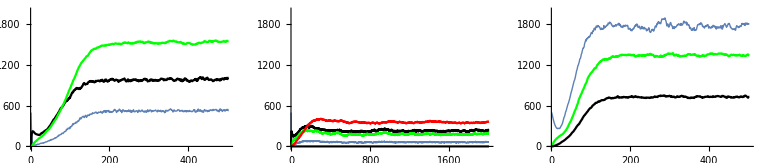

```mathematica
is = ImageSize->{Automatic,(2 72)};
pr = PlotRange->{{0,All},{0,2000}};
fign = ListLinePlot[datn/4,pr,PlotStyle->{Thin,Black, Green},LabelStyle->{Black,12},is];
figs = ListLinePlot[dats/4,pr,PlotStyle->{Thin,Black, Green,Red,Blue},LabelStyle->{Black,12},is];
figa = ListLinePlot[data/4,pr,PlotStyle->{Thin,Green,Black},LabelStyle->{Black,12},is];
GraphicsRow[{fign,figs,figa}]
```

```mathematica
lg3 = LineLegend[{Gray,Black,colA},{"Non-serotinous LP","Serotinous LP","Resprouting Aspen"}]
```

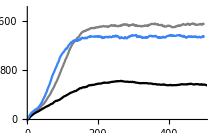

```mathematica
is = ImageSize->{Automatic,(2 72)};
pr = PlotRange->{{0,500},{0,1800}};
fig3a = ListLinePlot[{datn[[3]]/4,Total@dats[[{3,4}]]/4,data[[2]]/4} ,pr,PlotStyle->{Gray, Black,colA},LabelStyle->{Black,14},ImageSize->is5]
```

#### Recycle

```mathematica
type = "asym";datn = Transpose[Import["fig3/fig3_"<>type<>"_com_PN0_p_0.8_FFI_100_U_200_rep_1.counts","Table"][[2;;,{4,5,6}]]];
dats = Transpose[Import["fig3/fig3_"<>type<>"_com_PS0_p_0.8_FFI_100_U_200_rep_1.counts","Table"][[2;;-2,{7,8,9,10,11}]]];
data = Transpose[Import["fig3/fig3_"<>type<>"_com_AA0_p_0.8_FFI_100_U_200_rep_1.counts","Table"][[2;;-2,{12,13,14}]]];
```

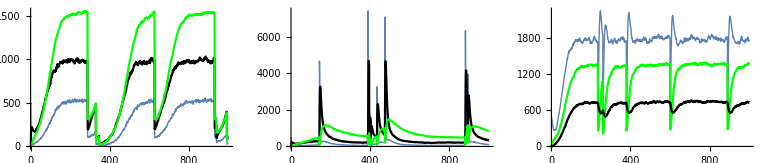

```mathematica
is = ImageSize->{Automatic,(2 72)};
pr = PlotRange->{{0,All},{0,All}};
fign = ListLinePlot[datn/4,pr,PlotStyle->{Thin,Black, Green},LabelStyle->{Black,12},is];
figs = ListLinePlot[{dats[[1]],dats[[2]],Total@dats[[{3,4}]]}/4,pr,PlotStyle->{Thin,Black, Green,Red,Blue},LabelStyle->{Black,12},is];
figa = ListLinePlot[data/4,pr,PlotStyle->{Thin,Green,Black},LabelStyle->{Black,12},is];
GraphicsRow[{fign,figs,figa}]
```

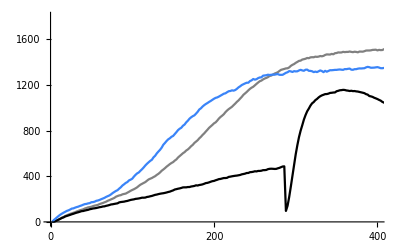

```mathematica
is = ImageSize->{Automatic,(2 72)};
tx = Ticks->{{Range[0,300,50],Range[0,600,100]}//Transpose,Automatic};
pr = PlotRange->{{0,200},{0,1800}};
fig3a = ListLinePlot[{datn[[3]]/4,Total@dats[[{3,4}]]/4,data[[2]]/4} ,pr,PlotStyle->{Gray, Black,colA},LabelStyle->{Black,12},is,tx]
```

### Figure 3 without competition with fire

#### Model definition

The model is modified here and should not be used anywhere else.  I removed interspecific competition below because I want a plot with three responses for the same type of fire.

```mathematica
(* Initial conditions *)

icN = Import["fig3/init_com_PN.txt","Table"];
icS = Import["fig3/init_com_PS.txt","Table"];
icA = Import["fig3/init_com_AA.txt","Table"];

iALLnoCC = Join[icN,icS,icA];
Export["fig3/ALL_noCC.txt",iALLnoCC,"Table"];
```

```mathematica
Map[Length, {icN, icS,icA, iALLnoCC}]
```

{12248,3485,15809,31542}

```mathematica
PF  = {{0.8,200}};
sym =False; 
case =1;
PBURN = PF[[case,1]]; FFI = PF[[case,2]];
If[sym ==True,
PMT = SPMT; type = "sym",
PMT = APMT;type = "asym"];
T = 1000;
U =200;
Do[
TEXTSIM = {"#!/bin/bash "};
Do[

(* scaling the fire related rate with domain size *) 
scaledB =DecimalForm[1./(ffi U^2)]; (*gives the per area fire occurrence*)
firerad =N@Sqrt[pburn U^2/ Pi]; (* define fire size wrt to area burn*)
scaledmF = DecimalForm[N[firerad^2 Pi PMT["F","mF"]]]; (* this is the height of the fire kernel *)

(* model definition *)
text= 
{
(* for non-serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["n1","n3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n2","n1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n3","n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["n1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","n3","pP"],

(* for serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s2","s1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s3","s2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s4","s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["s1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s3","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s4","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","s4"],

(* for aspen without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["a2","a4"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a3","a2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a4","a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["a2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","a3","aA"],

(*(* interspecific competition *)
(* between adult pines *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s4","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s4"],
(* adult pine to juvenile and adult aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","n3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","n3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s4","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s4","AP"],
(* adult aspen to juveline and adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a3","PA"],
(* adult pine to aspen root *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","n3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s4","RP"],
(* aspen root to adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a4","PR"],*)

(* fire *)
Immigration[SpCode[#],scaledB]&["F"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["F"],

(* non-serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n3","F"],

(* serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s3","F"],
ChangeToAnotherTypeByCombustion[SpCode[#1],SpCode[#2],SpCode[#3],tophat[scaledmF,firerad]]&["s5","s4","F"],
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s5"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["s5"],

(* aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a3","F"]
};

text=Map[ToString,text];
Export["fig3/model_special_noCC_"<>type<>"_p_"<>ToString@pburn<>"_FFI_"<>ToString@ffi<>"_U_"<>ToString@U<>".txt",text];
,{ffi ,{FFI}},{pburn,{PBURN}}];
,{rep,1}];

rep =1;
Do[
TEXTSIM = {"#!/bin/bash "};
textsim  = 
"time ./goldilocks_sim -p processes.txt -m model_special_noCC_"<>type<>"_p_"<>ToString@PBURN<>"_FFI_"<>ToString@FFI<>"_U_"<>ToString@U<>".txt -i "<>com<>".txt -oute 0 -outc 0 -o fig3_"<>type<>"_com_"<>com<>"_p_"<>ToString@PBURN<>"_FFI_"<>ToString@FFI<>"_U_"<>ToString@U<>"_rep_"<>ToString@rep<>" -r "<>ToString@rep<>" -U "<>ToString@U<>" -T "<>ToString@T<>" -dT 1 -w "<>ToString[Ceiling[30]];
AppendTo[TEXTSIM, textsim];
Export["fig3/fig3_"<>type<>"_"<>com<>"_p_"<>ToString@PBURN<>"_FFI_"<>ToString@FFI<>"_T_"<>ToString@T<>".txt",TEXTSIM];
,{com ,{"ALL_noCC"}}];


Clear[PMT];
```

#### Visualization

```mathematica
type = "asym";
datn = Transpose[Import["fig3/fig3_asym_com_ALL_noCC_p_0.8_FFI_200_U_200_rep_1.counts","Table"][[2;;,{4,5,6}]]];
dats = Transpose[Import["fig3/fig3_asym_com_ALL_noCC_p_0.8_FFI_200_U_200_rep_1.counts","Table"][[2;;,{7,8,9,10,11}]]];
data = Transpose[Import["fig3/fig3_asym_com_ALL_noCC_p_0.8_FFI_200_U_200_rep_1.counts","Table"][[2;;,{12,13,14}]]];
```

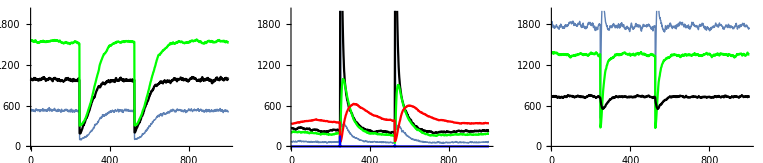

```mathematica
is = ImageSize->{Automatic,(2 72)};
pr = PlotRange->{{0,All},{0,2000}};
fign = ListLinePlot[datn/4,pr,PlotStyle->{Thin,Black, Green},LabelStyle->{Black,12},is];
figs = ListLinePlot[dats/4,pr,PlotStyle->{Thin,Black, Green,Red,Blue},LabelStyle->{Black,12},is];
figa = ListLinePlot[data/4,pr,PlotStyle->{Thin,Green,Black},LabelStyle->{Black,12},is];
GraphicsRow[{fign,figs,figa}]
```

```mathematica
lg3 = LineLegend[{Gray,Black,colA},{"Non-serotinous LP","Serotinous LP","Resprouting Aspen"}]
```

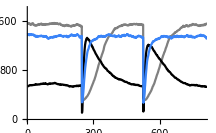

```mathematica
is = ImageSize->{Automatic,(2 72)};
pr = PlotRange->{{0,800},{0,1800}};
fig3c = ListLinePlot[{datn[[3]]/4,Total@dats[[{3,4}]]/4,data[[2]]/4} ,pr,PlotStyle->{Gray, Black,colA},LabelStyle->{Black,14},ImageSize-> is5]
```

#### Recycle

```mathematica
type = "asym";datn = Transpose[Import["fig3/fig3_"<>type<>"_com_PN0_p_0.8_FFI_100_U_200_rep_1.counts","Table"][[2;;,{4,5,6}]]];
dats = Transpose[Import["fig3/fig3_"<>type<>"_com_PS0_p_0.8_FFI_100_U_200_rep_1.counts","Table"][[2;;-2,{7,8,9,10,11}]]];
data = Transpose[Import["fig3/fig3_"<>type<>"_com_AA0_p_0.8_FFI_100_U_200_rep_1.counts","Table"][[2;;-2,{12,13,14}]]];
```

```mathematica
is = ImageSize->{Automatic,(2 72)};
pr = PlotRange->{{0,All},{0,All}};
fign = ListLinePlot[datn/4,pr,PlotStyle->{Thin,Black, Green},LabelStyle->{Black,12},is];
figs = ListLinePlot[{dats[[1]],dats[[2]],Total@dats[[{3,4}]]}/4,pr,PlotStyle->{Thin,Black, Green,Red,Blue},LabelStyle->{Black,12},is];
figa = ListLinePlot[data/4,pr,PlotStyle->{Thin,Green,Black},LabelStyle->{Black,12},is];
GraphicsRow[{fign,figs,figa}]
```

-Graphics-

```mathematica
is = ImageSize->{Automatic,(2 72)};
tx = Ticks->{{Range[0,300,50],Range[0,600,100]}//Transpose,Automatic};
pr = PlotRange->{{0,200},{0,1800}};
fig3a = ListLinePlot[{datn[[3]]/4,Total@dats[[{3,4}]]/4,data[[2]]/4} ,pr,PlotStyle->{Gray, Black,colA},LabelStyle->{Black,12},is,tx]
```

-Graphics-

### Figure 3 with symmetric competition

#### Model definition

```mathematica
PF  = {{0,100000},{0.8,100},{0.8,200}};
```

```mathematica
sym =True; 
case =3;
PBURN = PF[[case,1]]; FFI = PF[[case,2]];
If[sym ==True,
PMT = SPMT; type = "sym",
PMT = APMT;type = "asym"];
T = 1500;
U =200;
Do[
TEXTSIM = {"#!/bin/bash "};
Do[

(* scaling the fire related rate with domain size *) 
scaledB =DecimalForm[1./(ffi U^2)]; (*gives the per area fire occurrence*)
firerad =N@Sqrt[pburn U^2/ Pi]; (* define fire size wrt to area burn*)
scaledmF = DecimalForm[N[firerad^2 Pi PMT["F","mF"]]]; (* this is the height of the fire kernel *)

(* model definition *)
text= 
{
(* for non-serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["n1","n3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n2","n1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n3","n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["n1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","n3","pP"],

(* for serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s2","s1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s3","s2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s4","s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["s1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s3","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s4","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","s4"],

(* for aspen without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["a2","a4"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a3","a2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a4","a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["a2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","a3","aA"],

(* interspecific competition *)
(* between adult pines *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s4","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s4"],
(* adult pine to juvenile and adult aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","n3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","n3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s4","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s4","AP"],
(* adult aspen to juveline and adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a3","PA"],
(* adult pine to aspen root *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","n3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s4","RP"],
(* aspen root to adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a4","PR"],

(* fire *)
Immigration[SpCode[#],scaledB]&["F"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["F"],

(* non-serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n3","F"],

(* serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s3","F"],
ChangeToAnotherTypeByCombustion[SpCode[#1],SpCode[#2],SpCode[#3],tophat[scaledmF,firerad]]&["s5","s4","F"],
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"] fb,PMT[#2,"Kb"]]] &["s1","s5"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["s5"],

(* aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a3","F"]
};

text=Map[ToString,text];
Export["fig3/model_"<>type<>"_b_"<>ToString@fb<>"_p_"<>ToString@pburn<>"_ffi_"<>ToString@ffi<>"_U_"<>ToString@U<>".txt",text];
,{ffi ,{FFI}},{pburn,{PBURN}},{fb, {1,0.5,0.2}}];
,{rep,1}];

rep =1;
TEXTSIM = {"#!/bin/bash "};
Do[
textsim  = 
"time ./goldilocks_sim -p processes.txt -m model_"<>type<>"_b_"<>ToString@fb<>"_p_"<>ToString@PBURN<>"_ffi_"<>ToString@FFI<>"_U_"<>ToString@U<>".txt -i init_com_ALL.txt -oute 0 -outc 0 -o fig3_"<>type<>"_b_"<>ToString@fb<>"_com_ALL_p_"<>ToString@PBURN<>"_ffi_"<>ToString@FFI<>"_U_"<>ToString@U<>"_rep_"<>ToString@rep<>" -r "<>ToString@rep<>" -U "<>ToString@U<>" -T "<>ToString@T<>" -dT 1 -w "<>ToString[Ceiling[30]];
AppendTo[TEXTSIM, textsim];
Export["fig3/fig3_"<>type<>"_com_ALL_p_"<>ToString@PBURN<>"_ffi_"<>ToString@FFI<>"_T_"<>ToString@T<>".txt",TEXTSIM];
,{fb, {1,0.5,0.2}}];


Clear[PMT];
```

#### Visualization

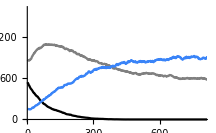

```mathematica
dat =Import["fig3/fig3_sym_b_1_com_ALL_p_0_ffi_100000_U_200_rep_1.counts","Table"][[2;;,{6,9,10,13}]]//Transpose;
sfig3a = ListPlot[{dat[[1]],Total@dat[[{2,3}]],dat[[4]]}/4, PlotStyle->{Gray, Black, colA},Joined->True,PlotRange->{{0,800},{0,1600}},LabelStyle->{Black,14},ImageSize->is5]
```

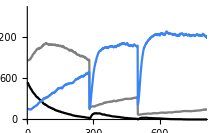

```mathematica
dat =Import["fig3/fig3_sym_b_1_com_ALL_p_0.8_ffi_200_U_200_rep_1.counts","Table"][[2;;,{6,9,10,13}]]//Transpose;
sfig3b = ListPlot[{dat[[1]],Total@dat[[{2,3}]],dat[[4]]}/4, PlotStyle->{Gray, Black, colA},Joined->True,PlotRange->{{0,800},{0,1600}},LabelStyle->{Black,14},ImageSize->is5]
```

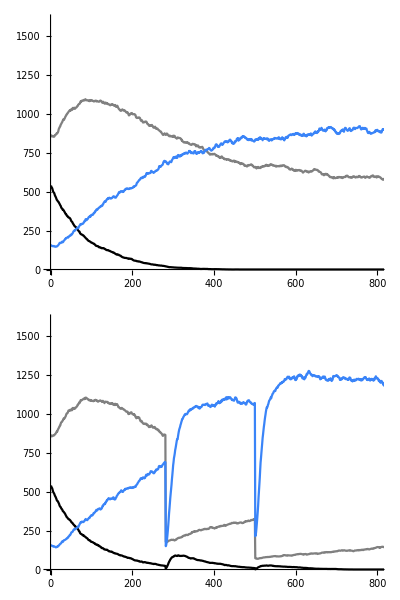

```mathematica
FigS4 = Grid[{{sfig3a,sfig3b}}//Transpose]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/FigS4.jpg",FigS4, ImageResolution->200];
```

#### Recycle: for p = 0.8 and FFI = 100

```mathematica
dat =Import["fig3/fig3_sym_b_0.5_com_ALL_p_0.8_ffi_100_U_200_rep_1.counts","Table"][[2;;,{6,9,10,13}]]//Transpose;
```

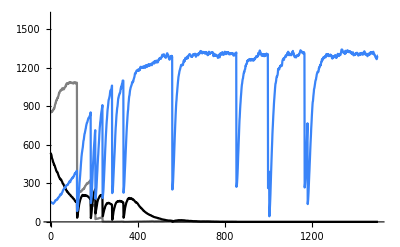

```mathematica
ListPlot[{dat[[1]],Total@dat[[{2,3}]],dat[[4]]}/4, PlotStyle->{Gray, Black, colA},Joined->True,PlotRange->{{0,1500},{0,1600}},LabelStyle->14]
```

```mathematica
dat =Import["fig3/fig3_asym_b_0.5_com_ALL_p_0.8_ffi_100_U_200_rep_1.counts","Table"][[2;;,{6,9,10,13}]]//Transpose;
```

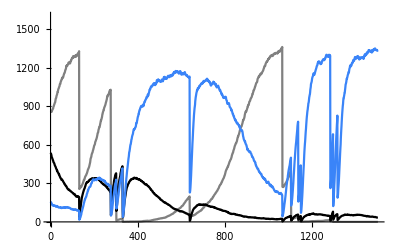

```mathematica
ListPlot[{dat[[1]],Total@dat[[{2,3}]],dat[[4]]}/4, PlotStyle->{Gray, Black, colA},Joined->True,PlotRange->{{0,1500},{0,1600}},LabelStyle->14]
```

### Figure 3df with asymmetric competition

#### Model definition

```mathematica
PF  = {{0,100000},{0.8,100},{0.8,200}};
```

```mathematica
sym =False; 
case =3;
PBURN = PF[[case,1]]; FFI = PF[[case,2]];
If[sym ==True,
PMT = SPMT; type = "sym",
PMT = APMT;type = "asym"];
T = 1500;
U =200;
Do[
TEXTSIM = {"#!/bin/bash "};
Do[

(* scaling the fire related rate with domain size *) 
scaledB =DecimalForm[1./(ffi U^2)]; (*gives the per area fire occurrence*)
firerad =N@Sqrt[pburn U^2/ Pi]; (* define fire size wrt to area burn*)
scaledmF = DecimalForm[N[firerad^2 Pi PMT["F","mF"]]]; (* this is the height of the fire kernel *)

(* model definition *)
text= 
{
(* for non-serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["n1","n3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n2","n1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n3","n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["n1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","n3","pP"],

(* for serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s2","s1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s3","s2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s4","s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["s1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s3","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s4","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","s4"],

(* for aspen without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["a2","a4"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a3","a2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a4","a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["a2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","a3","aA"],

(* interspecific competition *)
(* between adult pines *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s4","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s4"],
(* adult pine to juvenile and adult aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","n3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","n3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s4","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s4","AP"],
(* adult aspen to juveline and adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a3","PA"],
(* adult pine to aspen root *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","n3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s4","RP"],
(* aspen root to adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a4","PR"],

(* fire *)
Immigration[SpCode[#],scaledB]&["F"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["F"],

(* non-serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n3","F"],

(* serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s3","F"],
ChangeToAnotherTypeByCombustion[SpCode[#1],SpCode[#2],SpCode[#3],tophat[scaledmF,firerad]]&["s5","s4","F"],
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"] fb,PMT[#2,"Kb"]]] &["s1","s5"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["s5"],

(* aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a3","F"]
};

text=Map[ToString,text];
Export["fig3/model_"<>type<>"_b_"<>ToString@fb<>"_p_"<>ToString@pburn<>"_ffi_"<>ToString@ffi<>"_U_"<>ToString@U<>".txt",text];
,{ffi ,{FFI}},{pburn,{PBURN}},{fb, {1,0.5,0.2}}];
,{rep,1}];

rep =1;
TEXTSIM = {"#!/bin/bash "};
Do[
textsim  = 
"time ./goldilocks_sim -p processes.txt -m model_"<>type<>"_b_"<>ToString@fb<>"_p_"<>ToString@PBURN<>"_ffi_"<>ToString@FFI<>"_U_"<>ToString@U<>".txt -i init_com_ALL.txt -oute 0 -outc 0 -o fig3_"<>type<>"_b_"<>ToString@fb<>"_com_ALL_p_"<>ToString@PBURN<>"_ffi_"<>ToString@FFI<>"_U_"<>ToString@U<>"_rep_"<>ToString@rep<>" -r "<>ToString@rep<>" -U "<>ToString@U<>" -T "<>ToString@T<>" -dT 1 -w "<>ToString[Ceiling[30]];
AppendTo[TEXTSIM, textsim];
Export["fig3/fig3_"<>type<>"_com_ALL_p_"<>ToString@PBURN<>"_ffi_"<>ToString@FFI<>"_T_"<>ToString@T<>".txt",TEXTSIM];
,{fb, {1,0.5,0.2}}];


Clear[PMT];
```

#### Visualization

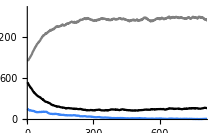

```mathematica
dat =Import["fig3/fig3_asym_b_1_com_ALL_p_0_ffi_100000_U_200_rep_1.counts","Table"][[2;;,{6,9,10,13}]]//Transpose;

fig3b = ListPlot[{dat[[1]],Total@dat[[{2,3}]],dat[[4]]}/4, PlotStyle->{Gray, Black, colA},Joined->True,PlotRange->{{0,800},{0,1600}},LabelStyle->{Black,14},ImageSize-> is5]
```

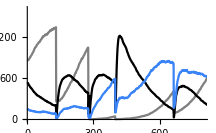

```mathematica
dat =Import["fig3/fig3_asym_b_1_com_ALL_p_0.8_ffi_200_U_200_rep_1.counts","Table"][[2;;,{6,9,10,13}]]//Transpose;

fig3d = ListPlot[{dat[[1]],Total@dat[[{2,3}]],dat[[4]]}/4, PlotStyle->{Gray, Black, colA},Joined->True,PlotRange->{{0,800},{0,1600}},LabelStyle->{Black,14},ImageSize -> is5]
```

#### Recycle

```mathematica
dat =Import["fig3/fig3_sym_b_0.5_com_ALL_p_0.8_ffi_100_U_200_rep_1.counts","Table"][[2;;,{6,9,10,13}]]//Transpose;
```

```mathematica
ListPlot[{dat[[1]],Total@dat[[{2,3}]],dat[[4]]}/4, PlotStyle->{Gray, Black, colA},Joined->True,PlotRange->{{0,1500},{0,1600}},LabelStyle->14]
```

-Graphics-

```mathematica
dat =Import["fig3/fig3_asym_b_0.5_com_ALL_p_0.8_ffi_100_U_200_rep_1.counts","Table"][[2;;,{6,9,10,13}]]//Transpose;
```

```mathematica
ListPlot[{dat[[1]],Total@dat[[{2,3}]],dat[[4]]}/4, PlotStyle->{Gray, Black, colA},Joined->True,PlotRange->{{0,1500},{0,1600}},LabelStyle->14]
```

-Graphics-

## Figures 4 and 5: contour plots all cases

#### Model definition

```mathematica
(* Discretization of parameter space for proportion burned and fire free interval *)
PBURN =Range[0.05,0.95,0.1];
FFI = Flatten[{5,10,15,Range[20,100,10]}];
```

```mathematica
(* these are used as input for parallelization *)
fctrs = Table[{ToExpression[icom],type,fb, ToString@PBURN[[i]],ffi,rep},{icom, {"PN","AA","PS"}},{fb,{1}},{i,Length@PBURN},{ffi,FFI}, {rep,5},{type,{"sym"}}];
fctrs2 = Table[{ToExpression[icom],type,fb, ToString@PBURN[[i]],ffi,rep},{icom, {"PS"}},{fb,{0.5,0.2}},{i,Length@PBURN},{ffi,FFI}, {rep,5},{type,{"sym"}}];
fctrs3 = Table[{ToExpression[icom],type,fb, ToString@PBURN[[i]],ffi,rep},{icom, {"ALL"}},{type,{"sym","asym"}},{fb,{1,0.5,0.2}},{i,Length@PBURN},{ffi,FFI}, {rep,5}];
FCT = Partition[Flatten[{fctrs,fctrs2,fctrs3}],6];
```

```mathematica
Export["fig6/fig5_factors.txt",FCT,"Table"];
Export["fig6/fig5_factors_test.txt",FCT[[{541,547}]],"Table"];
```

```mathematica
(* Change format of initial conditions *)
```

```mathematica
dat = Import["fig6/fig3_asym_com_AA0_init", "Table"];
Export["fig6/init_com_AA.txt",dat,"Table"];

dat = Import["fig6/fig3_asym_com_PS0_init", "Table"];
Export["fig6/init_com_PS.txt",dat,"Table"];

dat = Import["fig6/fig3_asym_com_PN0_init", "Table"];
Export["fig6/init_com_PN.txt",dat,"Table"];
```

```mathematica
(* 
type = asymmetric or symmetric;
fb= fraction of seedbank for serotinous;
PBURN = proportion burned;
ffi = fire free interval
*)
subFCT = Table[{type,fb, PBURN[[i]],ffi},{fb,{1,0.5,0.2}},{i,Length@PBURN},{ffi,FFI},{type,{"sym","asym"}}];
subFCT = Partition[Flatten[subFCT],4];
```

```mathematica
(* general all the model definitions for all models *)
T = 1500;
U =200;
Do[
Clear[PMT];
type = fct[[1]];
fb = fct[[2]];
pburn = fct[[3]];
ffi = fct[[4]];

PMT = If[type == "sym",
 SPMT,
 APMT];

TEXTSIM = {"#!/bin/bash "};
(* scaling the fire related rate with domain size *) 
scaledB =DecimalForm[1./(ffi U^2)]; (*gives the per area fire occurrence*)
firerad =N@Sqrt[pburn U^2/ Pi]; (* define fire size wrt to area burn*)
scaledmF = DecimalForm[N[firerad^2 Pi PMT["F","mF"]]]; (* this is the height of the fire kernel *)
(* model definition *)
text= 
{
(* for non-serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["n1","n3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n2","n1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n3","n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["n1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","n3","pP"],

(* for serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s2","s1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s3","s2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s4","s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["s1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s3","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s4","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","s4"],

(* for aspen without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["a2","a4"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a3","a2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a4","a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["a2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","a3","aA"],

(* interspecific competition *)
(* between adult pines *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s4","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s4"],
(* adult pine to juvenile and adult aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","n3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","n3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s4","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s4","AP"],
(* adult aspen to juveline and adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a3","PA"],
(* adult pine to aspen root *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","n3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s4","RP"],
(* aspen root to adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a4","PR"],

(* fire *)
Immigration[SpCode[#],scaledB]&["F"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["F"],

(* non-serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n3","F"],

(* serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s3","F"],
ChangeToAnotherTypeByCombustion[SpCode[#1],SpCode[#2],SpCode[#3],tophat[scaledmF,firerad]]&["s5","s4","F"],
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"] fb,PMT[#2,"Kb"]]] &["s1","s5"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["s5"],

(* aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a3","F"]
};

text=Map[ToString,text];
Export["fig6/model_"<>type<>"_b_"<>ToString@fb<>"_p_"<>ToString@pburn<>"_ffi_"<>ToString@ffi<>"_U_"<>ToString@U<>".txt",text];
,{fct,subFCT}];
```

#### Compile data: computes the mean of the time series

This code calculates the mean density of each tree. When the length is smaller than 1450 it means that the tree went extinct and the values are set to zero. 
Notice that the values are divided by 4 to get from 200 x 200 to hectare

```mathematica
(* without competition*)
DDN =DDS1= DDS2 =DDS3 = DDA = {};
Do[
DN = DS1 =DS2 = DS3 = DA = ConstantArray[{},5];
Do[dn  =Import["fig6/fig5_sym_b_1_com_PN_p_"<>ToString@pp<>"_ffi_"<>ToString@ffi<>"_rep_"<>ToString@rep<>"_U_200_T_1500.counts","Table"][[2;;,6]];

If[Length@dn< 1450,
mn = 0., 
mn = Mean@dn[[500;;]]/4.;
];

ds1 = Total@Transpose[Import["fig6/fig5_sym_b_1_com_PS_p_"<>ToString@pp<>"_ffi_"<>ToString@ffi<>"_rep_"<>ToString@rep<>"_U_200_T_1500.counts","Table"][[2;;,{9,10}]]];

If[Length@ds1< 1450,
ms1= 0., 
ms1 =Mean@ds1[[500;;]]/4.;
];

ds2 = Total@Transpose[Import["fig6/fig5_sym_b_0.5_com_PS_p_"<>ToString@pp<>"_ffi_"<>ToString@ffi<>"_rep_"<>ToString@rep<>"_U_200_T_1500.counts","Table"][[2;;,{9,10}]]];

If[Length@ds2< 1450,
ms2= 0., 
ms2 = N@Mean@ds2[[500;;]]/4.;
];

ds3 = Total@Transpose[Import["fig6/fig5_sym_b_0.2_com_PS_p_"<>ToString@pp<>"_ffi_"<>ToString@ffi<>"_rep_"<>ToString@rep<>"_U_200_T_1500.counts","Table"][[2;;,{9,10}]]];

If[Length@ds3< 1450,
ms3= 0., 
ms3= Mean@ds3[[500;;]]/4.;
];

da =Import["fig6/fig5_sym_b_1_com_AA_p_"<>ToString@pp<>"_ffi_"<>ToString@ffi<>"_rep_"<>ToString@rep<>"_U_200_T_1500.counts","Table"][[2;;,13]];

If[Length@da< 1450,
ma= 0., 
ma= Mean@da[[500;;]]/4.;
];

DN[[rep]] =mn;
DS1[[rep]] =ms1;
DS2[[rep]] =ms2;
DS3[[rep]] =ms3;
DA[[rep]] =ma;

,{rep,5}];

AppendTo[DDN, {ffi,pp,Mean@DN}];
AppendTo[DDS1, {ffi,pp,Mean@DS1}];
AppendTo[DDS2, {ffi,pp,Mean@DS2}];
AppendTo[DDS3, {ffi,pp,Mean@DS3}];
AppendTo[DDA, {ffi,pp,Mean@DA}];

,{pp,PBURN},{ffi,FFI}];

Export["fig6/fig5_sym_b_1_noC_PN.csv",DDN];
Export["fig6/fig5_sym_b_1_noC_PS.csv",DDS1];
Export["fig6/fig5_sym_b_0.5_noC_PS.csv",DDS2];
Export["fig6/fig5_sym_b_0.2_noC_PS.csv",DDS3];
Export["fig6/fig5_sym_b_1_noC_AA.csv",DDA];
```

```mathematica
(* with competition *)
Do[
DATN= DATS =DATA = {};
Do[
MN = MS= MA = {};
Do[

dat = Import["fig6/fig5_"<>type<>"_b_"<>ToString@fb<>"_com_ALL_p_"<>ToString@pburn<>"_ffi_"<>ToString@ffi<>"_rep_"<>ToString@rep<>"_U_200_T_1500.counts"][[2;;,{6,9,10,13}]]//N;

If[Length@dat< 1450,
mn = 0.;ms = 0.;ma =0. ;, 
mn = Mean@dat[[500;;,1]]/4;
ms= Mean@Total[dat[[500;;,{2,3}]],{2}]/4;
ma = Mean@dat[[500;;,4]]/4;
];


AppendTo[MN,mn];
AppendTo[MS,ms];
AppendTo[MA,ma];
,{rep,5}];

AppendTo[DATN,{ffi,pburn,Mean@MN}];
AppendTo[DATS,{ffi,pburn,Mean@MS}];
AppendTo[DATA,{ffi,pburn,Mean@MA}];

,{pburn,PBURN},{ffi,FFI}];

Export["fig6/fig5_"<>type<>"_b_"<>ToString@fb<>"_ALL_PN.csv",DATN];
Export["fig6/fig5_"<>type<>"_b_"<>ToString@fb<>"_ALL_PS.csv",DATS];
Export["fig6/fig5_"<>type<>"_b_"<>ToString@fb<>"_ALL_AA.csv",DATA];
,{fb,FB},{type,{"sym","asym"}}];
```

#### Visualization

```mathematica
(*parameters for the plots, ls = legend size, pr = plot range*)
ls6 = 14; pr6 = {{5,100},{0.05,0.95},{0,1600}}; pr6a = {{5,100},{0.05,0.95},{0.03,1}};
```

```mathematica
dN = Import["fig6/fig5_sym_b_1_noC_PN.csv"];
dS1 = Import["fig6/fig5_sym_b_1_noC_PS.csv"];
dS2 = Import["fig6/fig5_sym_b_0.5_noC_PS.csv"];
dS3 = Import["fig6/fig5_sym_b_0.2_noC_PS.csv"];
dA= Import["fig6/fig5_sym_b_1_noC_AA.csv"];

(*when density is less than 50 then regenerations failed. The indeterminate allows to plot them as white space *)
 dN[[All,3]] = dN[[All,3]]/. (x_ /; x<50 -> Indeterminate);
 dS1[[All,3]] = dS1[[All,3]]/. (x_ /; x<50 -> Indeterminate);
 dS2[[All,3]] = dS2[[All,3]]/. (x_ /; x<50 -> Indeterminate);
 dS3[[All,3]] = dS3[[All,3]]/. (x_ /; x<50 -> Indeterminate);
 dA[[All,3]] = dA[[All,3]]/. (x_ /; x<50 -> Indeterminate);

(*dALL = {dN,dS1, dA};
dALL2 = {dS1,dS2, dS3};*)
```

```mathematica
pr4 = PlotRange-> {{5,100},{25.2,110},{0,1600}}; 
ls4 = LabelStyle-> Directive[Black,14];
```

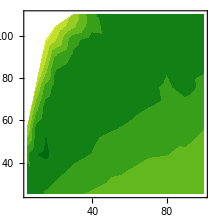
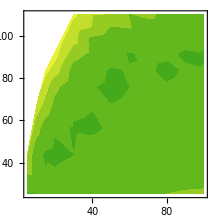
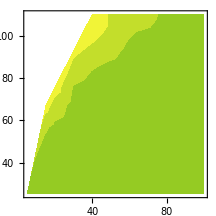
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
(* monospecific serotinous with three sizes of seedbank *)
fig4monoS = 
Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)pr4,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{dS1,dS2,dS3}}]
```

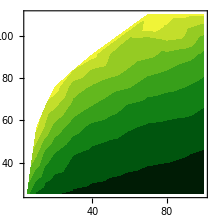
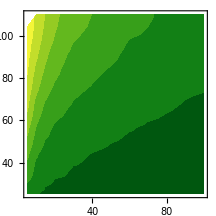
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
(* monospecific three strategies *)fig4monoAll = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)pr4,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{dN,dS1,dA}}]
```

```mathematica
daB1 = Table[Import["fig6/fig5_asym_b_1_ALL_"<>com<>".csv"],{com,{"PN","PS","AA"}}];
daB2 = Table[Import["fig6/fig5_asym_b_0.5_ALL_"<>com<>".csv"],{com,{"PN","PS","AA"}}];
daB3=Table[ Import["fig6/fig5_asym_b_0.2_ALL_"<>com<>".csv"],{com,{"PN","PS","AA"}}];

(* density for each species *)
{dcN,dcS,dcA}= daB1;

 dcN[[All,3]] = dcN[[All,3]]/. (x_ /; x<50 -> Indeterminate);
 dcS[[All,3]] = dcS[[All,3]]/. (x_ /; x<50 -> Indeterminate);
 dcA[[All,3]] = dcA[[All,3]]/. (x_ /; x<50 -> Indeterminate);

(* calculates the total density of trees *)
saC1 = daB1[[1]];
saC1[[All,3]]+= daB1[[2,All,3]]+daB1[[3,All,3]];
saC1[[All,3]] = saC1[[All,3]]/. (x_ /; x<50 -> Indeterminate);

saC2 = daB2[[1]];
saC2[[All,3]]+= daB2[[2,All,3]]+daB2[[3,All,3]];
saC2[[All,3]] = saC2[[All,3]]/. (x_ /; x<50 -> Indeterminate);

saC3 = daB3[[1]];
saC3[[All,3]]+=  daB3[[2,All,3]]+daB3[[3,All,3]];
saC3[[All,3]] = saC3[[All,3]]/. (x_ /; x<50 -> Indeterminate);

(* calculates the frequency of each strategy *)
paN1 = daB1[[1]];
paN1[[All,3]] = paN1[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paN1[[All,3]] /= saC1[[All,3]]]; 
paS1 = daB1[[2]];
paS1[[All,3]] = paS1[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paS1[[All,3]] /= saC1[[All,3]]]; 
paA1 = daB1[[3]];
paA1[[All,3]] = paA1[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paA1[[All,3]] /= saC1[[All,3]]]; 

paN2 = daB2[[1]];
paN2[[All,3]] = paN2[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paN2[[All,3]] /= saC2[[All,3]]]; 
paS2 = daB2[[2]];
paS2[[All,3]] = paS2[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paS2[[All,3]] /= saC2[[All,3]]]; 
paA2 = daB2[[3]];
paA2[[All,3]] = paA2[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paA2[[All,3]] /= saC2[[All,3]]]; 

paN3 = daB3[[1]];
paN3[[All,3]] = paN3[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paN3[[All,3]] /= saC3[[All,3]]]; 
paS3 = daB3[[2]];
paS3[[All,3]] = paS3[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paS3[[All,3]] /= saC3[[All,3]]]; 
paA3 = daB3[[3]];
paA3[[All,3]] = paA3[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[paA3[[All,3]] /= saC3[[All,3]]];
```

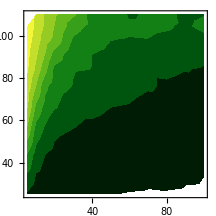
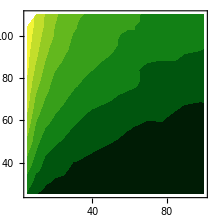
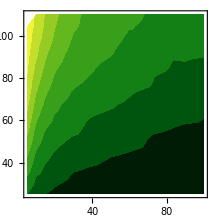
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
fig4mixed = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,pr4,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{saC1,saC2,saC3}}]
```

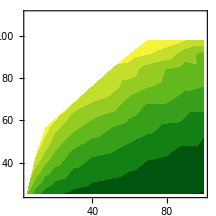
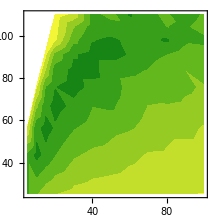
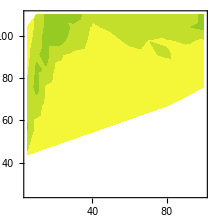
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
fig4ind = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,pr4,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{dcN,dcS,dcA}}]
```

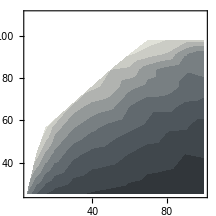
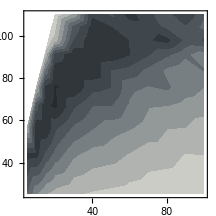
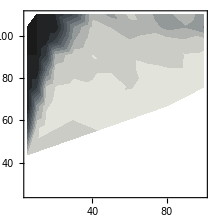
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
pr5 = PlotRange-> {{5,100},{25.2,110},{0.03,1}};

fig5LBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,pr5,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{paN1,paS1,paA1}}]
```

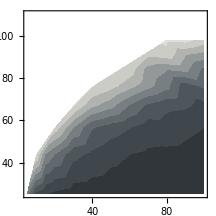
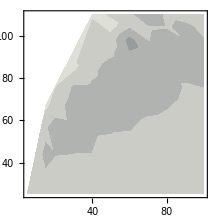
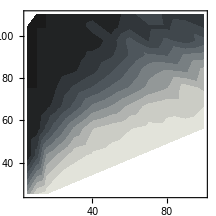
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
fig5IBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,pr5,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{paN2,paS2,paA2}}]
```

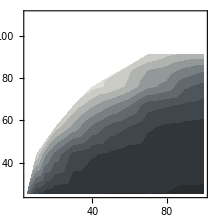
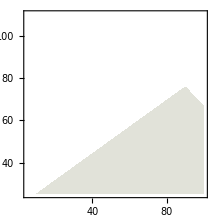
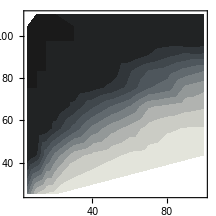
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
fig5SBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,pr5,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{paN3,paS3,paA3}}]
```

#### Visualization for symmetric case (for supplements)

```mathematica
dB1 = Table[Import["fig6/fig5_sym_b_1_ALL_"<>com<>".csv"],{com,{"PN","PS","AA"}}];
dB2 = Table[Import["fig6/fig5_sym_b_0.5_ALL_"<>com<>".csv"],{com,{"PN","PS","AA"}}];
dB3=Table[ Import["fig6/fig5_sym_b_0.2_ALL_"<>com<>".csv"],{com,{"PN","PS","AA"}}];

(* calculates the total density of trees *)
sC1 = dB1[[1]];
sC1[[All,3]]+= dB1[[2,All,3]]+dB1[[3,All,3]];
 sC1[[All,3]] = sC1[[All,3]]/. (x_ /; x<50 -> Indeterminate);

sC2 = dB2[[1]];
sC2[[All,3]]+= dB2[[2,All,3]]+dB2[[3,All,3]];
 sC2[[All,3]] = sC2[[All,3]]/. (x_ /; x<50 -> Indeterminate);

sC3 = dB3[[1]];
sC3[[All,3]]+=  dB3[[2,All,3]]+dB3[[3,All,3]];
 sC3[[All,3]] = sC3[[All,3]]/. (x_ /; x<50 -> Indeterminate);

(* calculates the frequency of each strategy *)
pN1 = dB1[[1]];
pN1[[All,3]] = pN1[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pN1[[All,3]] /= sC1[[All,3]]]; 
pS1 = dB1[[2]];
pS1[[All,3]] = pS1[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pS1[[All,3]] /= sC1[[All,3]]]; 
pA1 = dB1[[3]];
pA1[[All,3]] = pA1[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pA1[[All,3]] /= sC1[[All,3]]]; 

pN2 = dB2[[1]];
pN2[[All,3]] = pN2[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pN2[[All,3]] /= sC2[[All,3]]]; 
pS2 = dB2[[2]];
pS2[[All,3]] = pS2[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pS2[[All,3]] /= sC2[[All,3]]]; 
pA2 = dB2[[3]];
pA2[[All,3]] = pA2[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pA2[[All,3]] /= sC2[[All,3]]]; 

pN3 = dB3[[1]];
pN3[[All,3]] = pN3[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pN3[[All,3]] /= sC3[[All,3]]]; 
pS3 = dB3[[2]];
pS3[[All,3]] = pS3[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pS3[[All,3]] /= sC3[[All,3]]]; 
pA3 = dB3[[3]];
pA3[[All,3]] = pA3[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pA3[[All,3]] /= sC3[[All,3]]];
```

```mathematica
pr5
```

PlotRange→{{5,100},{25.2,110},{0.03,1}}

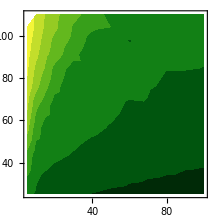
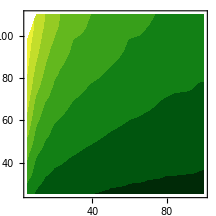
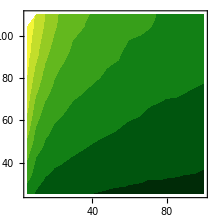
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
SfigSymVarBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)pr4,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{sC1,sC2,sC3}}]
```

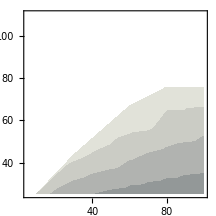
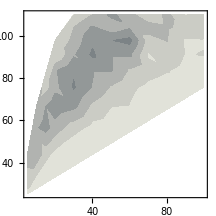
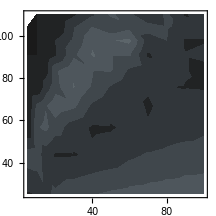
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
SfigLBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->2,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,pr5,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{pN1,pS1,pA1}}]
```

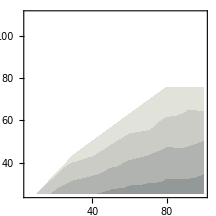
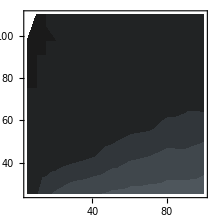
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
SfigIBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->2,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,pr5,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{pN2,(pS2/. Indeterminate->0.),pA2}}]
```

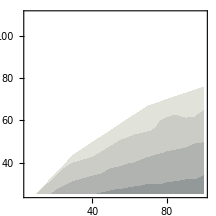
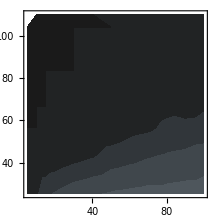
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
SfigSBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->2,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,pr5,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{pN3,(pS3/. Indeterminate->0.),pA3}}]
```

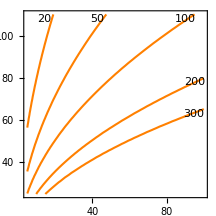
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
SFIGSymVarBankProp= Grid[{SfigLBank,SfigIBank,SfigIBank},Spacings->{1, 2}]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/SFigSymVarBankProp.jpg",SFIGSymVarBankProp, ImageResolution->200];
```

#### Recycle

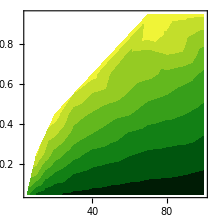
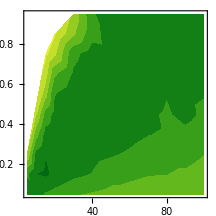
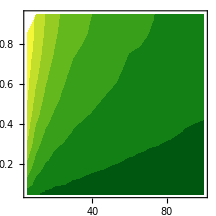

```mathematica
vfig4 = Table[ListContourPlot[i,ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)PlotRange->pr6,LabelStyle->ls6, ImageSize->is5,ContourStyle->None],{i,{dN,dS1,dA}}];
```

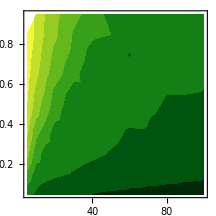
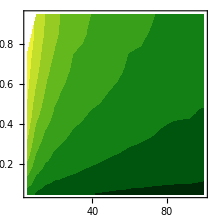
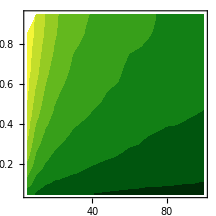

```mathematica
(* this uses proportion of area burned instead of fire diameter *)
fig6x1 = Table[ListContourPlot[i,ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)PlotRange->pr6,LabelStyle->ls6, ImageSize->is6,ContourStyle->None],{i,{sC1,sC2,sC3}}]
```

```mathematica
(* plot as function of fire rotation, different lines represent different areas burn *)

pr6z = {All,{0,1600}};
```

```mathematica
gBN1 = AddFRIGroupSize[dB1[[1]]];
gBN2 = AddFRIGroupSize[dB2[[1]]];
gBN3 = AddFRIGroupSize[dB3[[1]]];

gBS1 = AddFRIGroupSize[dB1[[2]]];
gBS2 = AddFRIGroupSize[dB2[[2]]];
gBS3 = AddFRIGroupSize[dB3[[2]]];

gBA1 = AddFRIGroupSize[dB1[[3]]];
gBA2 = AddFRIGroupSize[dB2[[3]]];
gBA3 = AddFRIGroupSize[dB3[[3]]];

fig6z=GraphicsGrid[
{{ListLogLinearPlot[Table[Callout[gBS1[i][[All,{3,4}]],i],{i, Keys@gBS1[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->{All,{0,500}}],
ListLogLinearPlot[Table[Callout[gBS2[i][[All,{3,4}]],i],{i, Keys@gBS2[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->{All,{0,500}}],
ListLogLinearPlot[Table[Callout[gBS3[i][[All,{3,4}]],i],{i, Keys@gBS3[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->{All,{0,500}}]},
{ListLogLinearPlot[Table[Callout[gBN1[i][[All,{3,4}]],i],{i, Keys@gBN1[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->{All,{0,500}}],
ListLogLinearPlot[Table[Callout[gBN2[i][[All,{3,4}]],i],{i, Keys@gBN2[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->{All,{0,500}}],
ListLogLinearPlot[Table[Callout[gBN3[i][[All,{3,4}]],i],{i, Keys@gBN3[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->{All,{0,500}}]},
{ListLogLinearPlot[Table[Callout[gBA1[i][[All,{3,4}]],i],{i, Keys@gBA1[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z],
ListLogLinearPlot[Table[Callout[gBA2[i][[All,{3,4}]],i],{i, Keys@gBA2[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z],
ListLogLinearPlot[Table[Callout[gBA3[i][[All,{3,4}]],i],{i, Keys@gBA3[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z]}}]
```

-Graphics-

```mathematica
gaBN1 = AddFRIGroupSize[daB1[[1]]];
gaBN2 = AddFRIGroupSize[daB2[[1]]];
gaBN3 = AddFRIGroupSize[daB3[[1]]];

gaBS1 = AddFRIGroupSize[daB1[[2]]];
gaBS2 = AddFRIGroupSize[daB2[[2]]];
gaBS3 = AddFRIGroupSize[daB3[[2]]];

gaBA1 = AddFRIGroupSize[daB1[[3]]];
gaBA2 = AddFRIGroupSize[daB2[[3]]];
gaBA3 = AddFRIGroupSize[daB3[[3]]];

fig7z =GraphicsGrid[{{ListLogLinearPlot[Table[Callout[gaBS1[i][[All,{3,4}]],i],{i, Keys@gaBS1[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z],
ListLogLinearPlot[Table[Callout[gaBS2[i][[All,{3,4}]],i],{i, Keys@gaBS2[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z],
ListLogLinearPlot[Table[Callout[gaBS3[i][[All,{3,4}]],i],{i, Keys@gaBS3[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z]},
{ListLogLinearPlot[Table[Callout[gaBN1[i][[All,{3,4}]],i],{i, Keys@gaBN1[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z],
ListLogLinearPlot[Table[Callout[gaBN2[i][[All,{3,4}]],i],{i, Keys@gaBN2[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z],
ListLogLinearPlot[Table[Callout[gaBN3[i][[All,{3,4}]],i],{i, Keys@gaBN3[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z]},
{ListLogLinearPlot[Table[Callout[gaBA1[i][[All,{3,4}]],i],{i, Keys@gaBA1[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z],
ListLogLinearPlot[Table[Callout[gaBA2[i][[All,{3,4}]],i],{i, Keys@gaBA2[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z],
ListLogLinearPlot[Table[Callout[gaBA3[i][[All,{3,4}]],i],{i, Keys@gaBA3[[{2,6,10}]]}],Joined-> True,ImageSize->is5,PlotRange->pr6z]}}]
```

-Graphics-

## Grouping figures

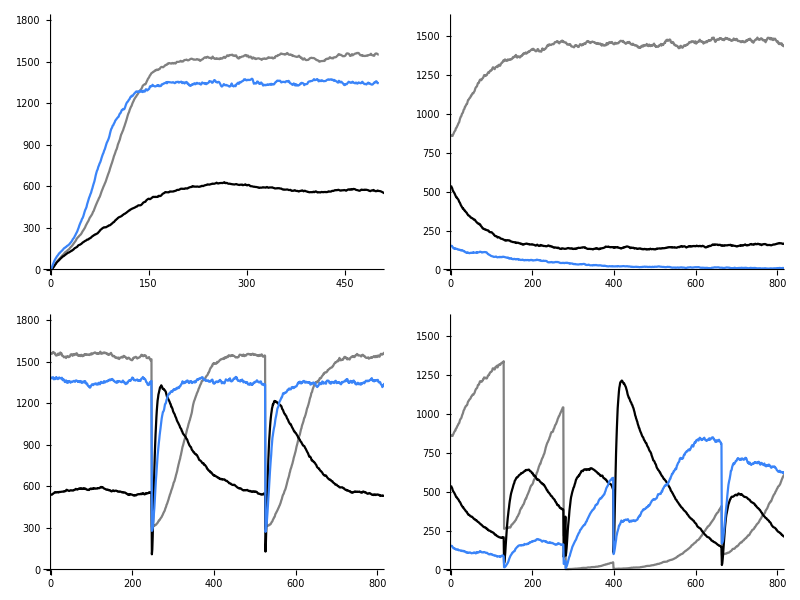

```mathematica
FIG3 = Grid[{{fig3a,fig3b},{fig3c,fig3d}},Spacings->{1,2}]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/Fig3.jpg",FIG3, ImageResolution->200];
```

```mathematica
fig4mixed
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
(*FIG4  = Grid[{fig4monoAll[[{1,2}]],{fig4monoAll[[3]],fig4mixed[[1]]}},Spacings-> {1,4}];*)
FIG4  = Grid[{fig4monoAll,fig4ind},Spacings-> {1,4}]
```

-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/Fig4.jpg",FIG4, ImageResolution->200];
```

```mathematica
FIG5  = Grid[{{fig4mixed[[1]],fig5LBank[[1]]},fig5LBank[[{2,3}]]},Spacings->{1,4}]
```

-Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/Fig5.jpg",FIG5, ImageResolution->200];
```

```mathematica
blA = BarLegend[{{"AvocadoColors","Reverse"},{0,1600}},7,LabelStyle->ls4]
```

```mathematica
FigS1 = Grid[{fig4monoS},Spacings->Automatic]
```

-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/FigS1.jpg",FigS1, ImageResolution->200];
```

```mathematica
SFigVarBank =Grid[{fig4monoS,fig4mixed}//Transpose,Spacings->{1, 2}]
```

-Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/SFigVarBank.jpg",SFigVarBank, ImageResolution->200];
```

```mathematica
xx ={fig5LBank,fig5IBank,fig5SBank}//Transpose;
xx = PrependTo[xx,fig4mixed];
```

```mathematica
FigS3  = Grid[xx//Transpose,Spacings->{1,1}]
```

-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/FigS3.jpg",FigS3, ImageResolution->200];
```

```mathematica
blF = BarLegend[{{"GrayTones","Reverse"},{0,1}},9,LabelStyle->ls5]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/legendF.jpg",blF, ImageResolution->200];
```

```mathematica
yy ={SfigLBank,SfigIBank,SfigIBank}//Transpose;
yy = PrependTo[yy,SfigSymVarBank ];
```

```mathematica
FigS5  = Grid[yy//Transpose,Spacings->{1,1}]
```

-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/FigS5.jpg",FigS5, ImageResolution->200];
```

## Supp Figure for just pines

#### Model definition

```mathematica
PBURN =Range[0.05,0.95,0.1];
FFI = Flatten[{5,10,15,Range[20,100,10]}];
```

```mathematica
fctrs2 = Table[{ToExpression[icom],type,fb, ToString@PBURN[[i]],ffi,rep},{icom, {"PP"}},{type,{"sym","asym"}},{fb,{1,0.5,0.2}},{i,Length@PBURN},{ffi,FFI}, {rep,5}];
FCT = Partition[Flatten[{fctrs2}],6];
```

```mathematica
Export["figS5_factors.txt",FCT,"Table"];
Export["figS5_factors_test.txt",FCT[[{541,547}]],"Table"];
```

```mathematica
SetDirectory[""];
fn = FileNames["fig5_*"];
NFCT ={};
Do[
name = "fig5_"<>fct[[2]]<>"_b_"<>ToString[fct[[3]]]<>"_com_"<>ToString@fct[[1]]<>"_p_"<>ToString@fct[[4]]<>"_ffi_"<>ToString@fct[[5]]<>"_rep_"<>ToString@fct[[6]]<>"_U_200_T_1500.counts";
If[MemberQ[fn, name]==False, AppendTo[NFCT, fct]];
,{fct, FCT}];
```

```mathematica
NFCT
```

{}

```mathematica
Export["figS5_2/figS5_factors_rest.txt",NFCT,"Table"];
```

```mathematica
subFCT = Table[{type,fb, PBURN[[i]],ffi},{fb,{1,0.5,0.2}},{i,Length@PBURN},{ffi,FFI},{type,{"sym","asym"}}];
subFCT = Partition[Flatten[subFCT],4];
```

```mathematica
T = 1500;
U =200;
Do[
Clear[PMT];
type = fct[[1]];
fb = fct[[2]];
pburn = fct[[3]];
ffi = fct[[4]];

PMT = If[type == "sym",
 SPMT,
 APMT];

TEXTSIM = {"#!/bin/bash "};
(* scaling the fire related rate with domain size *) 
scaledB =DecimalForm[1./(ffi U^2)]; (*gives the per area fire occurrence*)
firerad =N@Sqrt[pburn U^2/ Pi]; (* define fire size wrt to area burn*)
scaledmF = DecimalForm[N[firerad^2 Pi PMT["F","mF"]]]; (* this is the height of the fire kernel *)
(* model definition *)
text= 
{
(* for non-serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["n1","n3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n2","n1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["n3","n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["n1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["n3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","n3","pP"],

(* for serotinous without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["s1","s3"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s2","s1"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s3","s2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["s4","s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["s1"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["s4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["s4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s3","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","s4","pP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","s4"],

(* for aspen without fire and with inter-stage competition *)
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"],PMT[#2,"Kb"]]] &["a2","a4"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a3","a2"],
ChangeInType[SpCode[#1],SpCode[#2],PMT[#2,"g"]]&["a4","a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]] & ["a2"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a3"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]& ["a4"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a3"],
DeathByCompetition[SpCode[#],truncatedGaussian[PMT[#,"c"],PMT[#,"Kc"]]]&["a4"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","a3","aA"],

(* interspecific competition *)
(* between adult pines *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s3","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["s4","n3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s3"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"c"],PMT[#2,"Kc"]]]&["n3","s4"],
(* adult pine to juvenile and adult aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","n3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","n3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s3","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s3","AP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a2","s4","aP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a3","s4","AP"],
(* adult aspen to juveline and adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s2","a3","pA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a3","PA"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a3","PA"],
(* adult pine to aspen root *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","n3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s3","RP"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["a4","s4","RP"],
(* aspen root to adult pine *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["n3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s3","a4","PR"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#3,"cC"],PMT[#3,"KcC"]]]&["s4","a4","PR"],

(* fire *)
Immigration[SpCode[#],scaledB]&["F"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["F"],

(* non-serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["n3","F"],

(* serotinous *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s1","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["s3","F"],
ChangeToAnotherTypeByCombustion[SpCode[#1],SpCode[#2],SpCode[#3],tophat[scaledmF,firerad]]&["s5","s4","F"],
BirthToAnotherType[SpCode[#1],SpCode[#2],truncatedGaussian[PMT[#2,"b"] fb,PMT[#2,"Kb"]]] &["s1","s5"],
DensityIndependentDeath[SpCode[#],PMT[#,"m"]]&["s5"],

(* aspen *)
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a2","F"],
DeathByExternalFactor[SpCode[#1],SpCode[#2],tophat[scaledmF,firerad]]&["a3","F"]
};

text=Map[ToString,text];
Export["fig5/model_"<>type<>"_b_"<>ToString@fb<>"_p_"<>ToString@pburn<>"_ffi_"<>ToString@ffi<>"_U_"<>ToString@U<>".txt",text];
,{fct,subFCT}];
```

#### Compile data

```mathematica
(* with competition *)
Do[
DATN= DATS =(*DATA =*) {};
Do[
MN = MS=(* MA =*) {};
Do[

dat = Import["fig5/fig5_"<>type<>"_b_"<>ToString@fb<>"_com_PP_p_"<>ToString@pburn<>"_ffi_"<>ToString@ffi<>"_rep_"<>ToString@rep<>"_U_200_T_1500.counts"][[2;;,{6,9,10(*,13*)}]]//N;

If[Length@dat< 1450,
mn = 0.;ms = 0.;(*ma =0. ;*), 
mn = Mean@dat[[500;;,1]]/4;
ms= Mean@Total[dat[[500;;,{2,3}]],{2}]/4;
(*ma = Mean@dat[[500;;,4]]/4;*)
];


AppendTo[MN,mn];
AppendTo[MS,ms];
(*AppendTo[MA,ma];*)
,{rep,5}];

AppendTo[DATN,{ffi,pburn,Mean@MN}];
AppendTo[DATS,{ffi,pburn,Mean@MS}];
(*AppendTo[DATA,{ffi,pburn,Mean@MA}];*)

,{pburn,PBURN},{ffi,FFI}];

Export["fig5/fig5_"<>type<>"_b_"<>ToString@fb<>"_PP_PN.csv",DATN];
Export["fig5/fig5_"<>type<>"_b_"<>ToString@fb<>"_PP_PS.csv",DATS];
(*Export["/Users/tanjona/Documents/goldi_test/figS5_2/figS5_"<>type<>"_b_"<>ToString@fb<>"_noRoot_AA.csv",DATA];*)
,{fb,{1,0.5,0.2}},{type,{(*"sym",*)"asym"}}];
```

#### Visualization

```mathematica
is5 = 3 72;ls5 = 14; pr5 = {{5,100},{0.05,0.95},{50,1600}}; pr5b = {{5,100},{0.05,0.95},{10^(-6),1.}}; pr5a = {{5,100},{25.2,110},{50,1600}}; pr5ba = {{5,100},{25.2,110},{10^(-6),1.}};
```

```mathematica
dS1 = Import["fig6/fig5_sym_b_1_noC_PS.csv"];
dS2 = Import["fig6/fig5_sym_b_0.5_noC_PS.csv"];
dS3 = Import["fig6/fig5_sym_b_0.2_noC_PS.csv"];
dSALL = {dS1,dS2, dS3};

 dS1[[All,3]] = dS1[[All,3]]/. (x_ /; x<50 -> Indeterminate);
 dS2[[All,3]] = dS2[[All,3]]/. (x_ /; x<50 -> Indeterminate);
 dS3[[All,3]] = dS3[[All,3]]/. (x_ /; x<50 -> Indeterminate);
```

```mathematica
dC1 = Table[Import["fig5/figS5_sym_b_1_PP_"<>com<>".csv"],{com,{"PN","PS"(*,"AA"*)}}];
dC2 = Table[Import["fig5/figS5_sym_b_0.5_PP_"<>com<>".csv"],{com,{"PN","PS"(*,"AA"*)}}];
dC3=Table[ Import["fig5/figS5_sym_b_0.2_PP_"<>com<>".csv"],{com,{"PN","PS"(*,"AA"*)}}];

(* calculates the total density of trees *)
sC1 = dC1[[1]];
sC1[[All,3]]+= dC1[[2,All,3]];
 sC1[[All,3]] = sC1[[All,3]]/. (x_ /; x<50 -> Indeterminate);

sC2 = dC2[[1]];
sC2[[All,3]]+= dC2[[2,All,3]];
 sC2[[All,3]] = sC2[[All,3]]/. (x_ /; x<50 -> Indeterminate);

sC3 = dC3[[1]];
sC3[[All,3]]+= dC3[[2,All,3]];
 sC3[[All,3]] = sC3[[All,3]]/. (x_ /; x<50 -> Indeterminate);


(* calculates the frequency of serotinous trees *)
pC1 = dC1[[2]];
Quiet[pC1[[All,3]] /= sC1[[All,3]]]; 
pC1x = dC1[[1]];
 pC1x[[All,3]] = pC1x[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pC1x[[All,3]] /= sC1[[All,3]]]; 

pC2 = dC2[[2]];
Quiet[pC2[[All,3]] /= sC2[[All,3]]]; 
pC2x = dC2[[1]];
pC2x[[All,3]] = pC2x[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pC2x[[All,3]] /= sC1[[All,3]]]; 

pC3 = dC3[[2]];
Quiet[pC3[[All,3]] /= sC3[[All,3]]]; 
pC3x = dC3[[1]];
 pC3x[[All,3]] = pC3x[[All,3]]/. (x_ /; x<50 -> Indeterminate);
Quiet[pC3x[[All,3]] /= sC1[[All,3]]];
```

```mathematica
SfigPPVarBank =Table[Overlay[ {ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)pr4,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{sC1,sC2,sC3}}]
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
SfigPPVarBankS = Table[ Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,(*pr5,*)ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{pC1,pC2,pC3}}]
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
SfigPPVarBankN = Table[Overlay[{ ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->1,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,(*pr5,*)ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{pC1x,pC2x,pC3x}}]
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
FigS2 = Grid[{SfigPPVarBank,SfigPPVarBankN,SfigPPVarBankS}//Transpose,Spacings->{0.5, 0.5}]
```

-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export["/Users/tanjona/Box Sync/projects/ACES_goldilocks/figures/FigS2.jpg",FigS2, ImageResolution->200];
```

## Coexistence figure

```mathematica
pr5 = PlotRange-> {{5,100},{25.2,110},{0.03,1}};

fig5LBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->0,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,pr5,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{paN1,paS1,paA1}}]
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
fig4ind = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->0,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,pr4,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{dcN,dcS,dcA}}]
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
collateD = Append[Append[Transpose@dcN,dcS[[All,3]]], dcA[[All,3]]] //Transpose ;
```

```mathematica
cd = ColorData[#]&/@{{"AvocadoColors","Reverse"},{"CoffeeTones","Reverse"},{"GrayTones","Reverse"}};

(* color used for the coexistence plot*)
valp = 0.45;
colx = CMYKColor[0,0,0,valp];
colxy = CMYKColor[0,valp,0,valp];
colxyz = CMYKColor[valp,valp,0,valp];
coly = CMYKColor[0,valp,0,0];
colyz = CMYKColor[valp,valp,0,0];
colz =  CMYKColor[valp,0,0,0.];
colxz=  CMYKColor[valp,0,0,valp];


(* builds the color scheme for the coexistence by mapping a color to each communitu composition *)
et = 50;
CoexCol2[temp_]:= Which[
temp[[1]] ≥ et  && temp[[2]] ≥ et  && temp[[3]] ≥ et , colxyz,
temp[[1]] ≥ et && temp[[2]] ≥et && temp[[3]] <et,colxy,
temp[[1]] ≥ et && temp[[2]] < et&& temp[[3]] ≥ et, colxz ,
temp[[1]] < et && temp[[2]] ≥ et && temp[[3]] ≥ et,colyz ,
temp[[1]] ≥ et && temp[[2]] < et && temp[[3]] < et,colx,
temp[[1]] < et && temp[[2]] ≥et && temp[[3]] <et, coly,
temp[[1]] < et && temp[[2]] < et && temp[[3]] ≥ et, colz,
temp[[1]] < et && temp[[2]] < et && temp[[3]] < et, White
];
```

```mathematica
RES = {};
Do[
temp = collateD[[i,3;;]] /. Indeterminate-> 0.;
temp = CoexCol2[temp];
res = Flatten@{collateD[[i,{1,2}]],temp};
AppendTo[RES, res];
,{i, Length@collateD}];
```

```mathematica
RES2 =Reverse@Partition[RES[[All,-1]],12]
```

{{GrayLevel[1],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45]},{CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45]},{CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45]},{CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45]}}

```mathematica
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
```

```mathematica
(*figg = Labeled[ArrayPlot[RES2, AspectRatio->1,ImageSize->400(*, FrameTicks->True*)],Style[#, Black, 18,FontFamily->"Arial"] &/@{"Fire free interval", "Fire size"}, {Bottom,Left}, RotateLabel->True];*)
figg =ArrayPlot[RES2, AspectRatio->1,Frame->False]
```

-Graphics-

```mathematica
figArray = ContourPlot[1/(rr^2 Pi/200^2)ffi,{ffi,5,100},{rr,25,110}, Contours->{20,50,100,200,300 },ContourLabels->(Text[#3,{#1-3,#2-1},Background->White]&),ContourStyle->Directive[AbsoluteThickness[1.5],Orange],ContourShading-> None,LabelStyle->Directive[Black,14], ImageSize->is5 , Prolog->Inset[figg, Scaled[{0.5,0.5}], Scaled[{0.5,0.5}],Scaled[1]]]
```

-Graphics-

```mathematica
cout =  Rotate[#, 180 Degree]&/@(StringJoin@@@Subsets[{"N","S","A"},{1,3}])
```

{N,S,A,NS,NA,SA,NSA}

```mathematica
a=Disk[{0,1}];
b=Disk[{-0.5,0}];
c=Disk[{0.5,0}];
subsets=Subsets[{a,b,c},{1,3}];

subsetscolors= {colx,coly,colz,colxy,colxz,colyz,colxyz};

legFig2 = RegionPlot[Evaluate[DiscretizeRegion[RegionDifference[BooleanRegion[And,#],BooleanRegion[Or,Complement[{a,b,c,EmptyRegion[2]},#]]]]&/@subsets],PlotLabels->Callout[cout,Center, Background->LightBlue],Sequence[PlotStyle->subsetscolors,BoundaryStyle->Directive[Thickness[0.01],White],Frame->False,LabelStyle->{14},PerformanceGoal->"Speed",ImageSize->160]]
```

-Graphics-

```mathematica
cout
```

{N,S,A,NS,NA,SA,NSA}

```mathematica
figxx = Grid[{{figArray, Rotate[legFig2, 180 Degree]}},Spacings->2]
```

-Graphics- | -Graphics-

```mathematica
Export["/Users/tanjona/Documents/asa/projects/ACES_goldilocks/figures/fig_coex.png",figxx, ImageResolution-> 150]
```

/Users/tanjona/Documents/asa/projects/ACES_goldilocks/figures/fig_coex.png

```mathematica
460 {0.65, 0.02,0.015}
```

{299.,9.2,6.9}

# Recycle

```mathematica
pr5 = PlotRange-> {{5,100},{25.2,110},{0.03,1}};

fig5LBank = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->0,ColorFunction->(ColorData[{"GrayTones","Reverse"}]),ColorFunctionScaling->False,pr5,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{paN1,paS1,paA1}}]
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
fig4ind = Table[Overlay[{ListContourPlot[PropToRad[i],ScalingFunctions->{Automatic,Automatic},InterpolationOrder->0,ColorFunction->(ColorData[{"AvocadoColors","Reverse"}][Rescale[#,{0,1600}]]&),ColorFunctionScaling->False,pr4,ls4, ImageSize->is5,ContourStyle->None],cc}],{i,{dcN,dcS,dcA}}]
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
collateD = Append[Append[Transpose@dcN,dcS[[All,3]]], dcA[[All,3]]] //Transpose ;
```

```mathematica
collateD[[1]]/.Indeterminate-> 0.
```

{5,0.05,554.588,822.065,0.}

```mathematica
cd = ColorData[#]&/@{{"AvocadoColors","Reverse"},{"CoffeeTones","Reverse"},{"GrayTones","Reverse"}};

(* color used for the coexistence plot*)
valp = 0.45;
colx = CMYKColor[0,0,0,valp];
colxy = CMYKColor[0,valp,0,valp];
colxyz = CMYKColor[valp,valp,0,valp];
coly = CMYKColor[0,valp,0,0];
colyz = CMYKColor[valp,valp,0,0];
colz =  CMYKColor[valp,0,0,0.];
colxz=  CMYKColor[valp,0,0,valp];


(* builds the color scheme for the coexistence by mapping a color to each communitu composition *)
et = 50;
CoexCol2[temp_]:= Which[
temp[[1]] ≥ et  && temp[[2]] ≥ et  && temp[[3]] ≥ et , colxyz,
temp[[1]] ≥ et && temp[[2]] ≥et && temp[[3]] <et,colxy,
temp[[1]] ≥ et && temp[[2]] < et&& temp[[3]] ≥ et, colxz ,
temp[[1]] < et && temp[[2]] ≥ et && temp[[3]] ≥ et,colyz ,
temp[[1]] ≥ et && temp[[2]] < et && temp[[3]] < et,colx,
temp[[1]] < et && temp[[2]] ≥et && temp[[3]] <et, coly,
temp[[1]] < et && temp[[2]] < et && temp[[3]] ≥ et, colz,
temp[[1]] < et && temp[[2]] < et && temp[[3]] < et, White
];
```

```mathematica
RES = {};
Do[
temp = collateD[[i,3;;]] /. Indeterminate-> 0.;
temp = CoexCol2[temp];
res = Flatten@{collateD[[i,{1,2}]],temp};
AppendTo[RES, res];
,{i, Length@collateD}];
```

```mathematica
RES2 =Reverse@Partition[RES[[All,-1]],12]
```

{{GrayLevel[1],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45]},{CMYKColor[0.45, 0, 0, 0.],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45]},{CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0.45, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45]},{CMYKColor[0.45, 0.45, 0, 0],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45]},{CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45],CMYKColor[0, 0.45, 0, 0.45]}}

```mathematica
ArrayPlot[RES2, AspectRatio->1]
```

-Graphics-